```mathematica
FindFit[
{{6,3,-1,31.99},{7,3,0,39.24},{12,6,1,92.16},{15,8,0,111.95},{17,9,0,128.22},{40,20,1,342.05},{56,26,1,492.3},{107,47,0,915.2},{129,54,0,1087.6},{131,54,0,1103.5},{132,54,1,1112.4},{235,92,0,1783.8},{238,92,1,1801.6}}
,av A-as A^(2/3)-ac Z^2 A^(-1/3)-aa (A/2-Z)^2 A^-1+ap δ A^(-1/2),{av,as,ac,aa,ap},{A,Z,δ}]
```

{av→15.7094,as→17.0825,ac→0.743669,aa→86.311,ap→8.08955}

```mathematica
delta[a_,z_]:=If[OddQ[a],0,
				If[OddQ[z],-1,1]];
```

```mathematica
input=TableForm[Table[{a,z,delta[a,z],IsotopeData[{z,a},"BindingEnergy"]*a},{z,3,110},{a,IsotopeData[#,"MassNumber"]&/@IsotopeData[z]}],TableDepth->1]
```

{{3,3,0,6.8028},{4,3,-1,4.615044},{5,3,0,26.33066},{6,3,-1,31.99407},{7,3,0,39.24404},{8,3,-1,41.27666},{9,3,0,45.34055},{10,3,-1,45.31555},{11,3,0,45.64014},{12,3,-1,44.41}}
{{5,4,0,-0.7735},{6,4,1,26.92357},{7,4,0,37.6},{8,4,1,56.49948},{9,4,0,58.16482},{10,4,1,64.97711},{11,4,0,65.48104},{12,4,1,68.64991},{13,4,0,68.5499},{14,4,1,69.91456},{15,4,0,68.15},{16,4,1,68.34}}
{{6,5,-1,0.9126},{7,5,0,24.71914},{8,5,-1,37.73731},{9,5,0,56.3144},{10,5,-1,64.75071},{11,5,0,76.20482},{12,5,-1,79.57517},{13,5,0,84.45323},{14,5,-1,85.42303},{15,5,0,88.1857},{16,5,-1,88.14765},{17,5,0,89.52984},{18,5,-1,89.05},{19,5,0,90.08}}
{{8,6,1,24.782},{9,6,0,39.03728},{10,6,1,60.32041},{11,6,0,73.4401},{12,6,1,92.16173},{13,6,0,97.10804},{14,6,1,105.2845},{15,6,0,106.5025},{16,6,1,110.7529},{17,6,0,111.4795},{18,6,1,115.6634},{19,6,0,116.2403},{20,6,1,119.1747},{21,6,0,118.8},{22,6,1,119.6}}
{{10,7,-1,36.4366},{11,7,0,59.00449},{12,7,-1,74.0413},{13,7,0,94.10522},{14,7,-1,104.6586},{15,7,0,115.4919},{16,7,-1,117.981},{17,7,0,123.8646},{18,7,-1,126.693},{19,7,0,132.0165},{20,7,-1,134.185},{21,7,0,138.7701},{22,7,-1,140.0539},{23,7,0,141.8},{24,7,-1,140.7},{25,7,0,139.8}}
{{12,8,1,58.5491},{13,8,0,75.55592},{14,8,1,98.73231},{15,8,0,111.9554},{16,8,1,127.6193},{17,8,0,131.7624},{18,8,1,139.8065},{19,8,0,143.7614},{20,8,1,151.3701},{21,8,0,155.176},{22,8,1,162.0261},{23,8,0,164.769},{24,8,1,168.3824},{25,8,0,168.1},{26,8,1,167.9},{27,8,0,166.7},{28,8,1,165.9}}
{{14,9,-1,73.3},{15,9,0,97.25327},{16,9,-1,111.4197},{17,9,0,128.2196},{18,9,-1,137.3689},{19,9,0,147.8013},{20,9,-1,154.4026},{21,9,0,162.504},{22,9,-1,167.7345},{23,9,0,175.269},{24,9,-1,179.111},{25,9,0,183.4691},{26,9,-1,184.5413},{27,9,0,185.9576},{28,9,-1,185.7},{29,9,0,186.7},{30,9,-1,186.2},{31,9,0,186.9}}
{{16,10,1,97.32115},{17,10,0,112.928},{18,10,1,132.1431},{19,10,0,143.7801},{20,10,1,160.645},{21,10,0,167.406},{22,10,1,177.7702},{23,10,0,182.9709},{24,10,1,191.8397},{25,10,0,196.0675},{26,10,1,201.6012},{27,10,0,203.0321},{28,10,1,206.9288},{29,10,0,208.1869},{30,10,1,211.214},{31,10,0,211.5},{32,10,1,213.2},{33,10,0,212.5},{34,10,1,213.5}}
{{18,11,-1,112.4879},{19,11,0,131.8224},{20,11,-1,145.9728},{21,11,0,163.076},{22,11,-1,174.1456},{23,11,0,186.5643},{24,11,-1,193.5239},{25,11,0,202.5349},{26,11,-1,208.111},{27,11,0,214.8372},{28,11,-1,218.3803},{29,11,0,222.7974},{30,11,-1,225.1726},{31,11,0,228.9503},{32,11,-1,230.6119},{33,11,0,232.8584},{34,11,-1,233.1},{35,11,0,234.3},{36,11,-1,234.},{37,11,0,234.8}}
{{19,12,0,110.9268},{20,12,1,134.4678},{21,12,0,149.199},{22,12,1,168.5778},{23,12,0,181.7259},{24,12,1,198.257},{25,12,0,205.5876},{26,12,1,216.6807},{27,12,0,223.1241},{28,12,1,231.6274},{29,12,0,235.2991},{30,12,1,241.662},{31,12,0,244.04},{32,12,1,249.8488},{33,12,0,252.0712},{34,12,1,256.228},{35,12,0,257.},{36,12,1,259.7},{37,12,0,260.},{38,12,1,262.3},{39,12,0,261.8},{40,12,1,263.2}}
{{21,13,0,133.2},{22,13,-1,149.2},{23,13,0,168.7002},{24,13,-1,183.5981},{25,13,0,200.5286},{26,13,-1,211.894},{27,13,0,224.9517},{28,13,-1,232.6768},{29,13,0,242.113},{30,13,-1,247.8414},{31,13,0,254.9939},{32,13,-1,259.1736},{33,13,0,264.7123},{34,13,-1,267.1868},{35,13,0,272.4558},{36,13,-1,274.6149},{37,13,0,278.5219},{38,13,-1,280.4889},{39,13,0,283.2145},{40,13,-1,283.4},{41,13,0,285.},{42,13,-1,285.1}}
{{22,14,1,134.4},{23,14,0,150.9},{24,14,1,172.0041},{25,14,0,187.006},{26,14,1,206.046},{27,14,0,219.357},{28,14,1,236.5368},{29,14,0,245.0104},{30,14,1,255.6196},{31,14,0,262.207},{32,14,1,271.4102},{33,14,0,275.8933},{34,14,1,283.4287},{35,14,0,285.9036},{36,14,1,292.0971},{37,14,0,294.2659},{38,14,1,299.8245},{39,14,0,301.9003},{40,14,1,306.4328},{41,14,0,306.409},{42,14,1,309.6},{43,14,0,309.4},{44,14,1,311.3}}
{{24,15,-1,150.},{25,15,0,171.2},{26,15,-1,187.1},{27,15,0,206.9074},{28,15,-1,221.4204},{29,15,0,239.2856},{30,15,-1,250.6049},{31,15,0,262.9165},{32,15,-1,270.852},{33,15,0,280.9558},{34,15,-1,287.2473},{35,15,0,295.6186},{36,15,-1,299.0832},{37,15,0,305.8977},{38,15,-1,309.733},{39,15,0,315.92},{40,15,-1,319.2243},{41,15,0,324.4653},{42,15,-1,326.3213},{43,15,0,329.5655},{44,15,-1,331.3},{45,15,0,333.6},{46,15,-1,334.1}}
{{26,16,1,171.4},{27,16,0,187.9},{28,16,1,209.406},{29,16,0,224.7102},{30,16,1,243.6845},{31,16,0,256.7379},{32,16,1,271.7803},{33,16,0,280.4219},{34,16,1,291.839},{35,16,0,298.8249},{36,16,1,308.7139},{37,16,0,313.0176},{38,16,1,321.0537},{39,16,0,325.4261},{40,16,1,333.2017},{41,16,0,337.4256},{42,16,1,344.1553},{43,16,0,346.5143},{44,16,1,351.7366},{45,16,0,353.9444},{46,16,1,358.1},{47,16,0,358.8},{48,16,1,361.7},{49,16,0,361.}}
{{28,17,-1,186.1},{29,17,0,207.6},{30,17,-1,224.4},{31,17,0,243.9781},{32,17,-1,258.312},{33,17,0,274.057},{34,17,-1,285.5647},{35,17,0,298.2097},{36,17,-1,306.7894},{37,17,0,317.1},{38,17,-1,323.208},{39,17,0,331.2817},{40,17,-1,337.1106},{41,17,0,344.9313},{42,17,-1,350.6084},{43,17,0,357.9349},{44,17,-1,362.0691},{45,17,0,368.272},{46,17,-1,372.689},{47,17,0,376.6},{48,17,-1,378.8},{49,17,0,381.9},{50,17,-1,383.},{51,17,0,384.8}}
{{30,18,1,208.},{31,18,0,224.8},{32,18,1,246.4001},{33,18,0,261.655},{34,18,1,278.72},{35,18,0,291.4613},{36,18,1,306.7167},{37,18,0,315.5041},{38,18,1,327.3424},{39,18,0,333.9411},{40,18,1,343.8104},{41,18,0,349.9092},{42,18,1,359.3357},{43,18,0,364.9942},{44,18,1,373.7288},{45,18,0,378.8976},{46,18,1,386.9185},{47,18,0,391.1775},{48,18,1,397.1},{49,18,0,399.5},{50,18,1,404.},{51,18,0,405.3},{52,18,1,408.6},{53,18,0,409.1}}
{{32,19,-1,223.},{33,19,0,244.7},{34,19,-1,261.1},{35,19,0,278.8004},{36,19,-1,293.129},{37,19,0,308.5743},{38,19,-1,320.6462},{39,19,0,333.724},{40,19,-1,341.5233},{41,19,0,351.6185},{42,19,-1,359.1523},{43,19,0,368.7953},{44,19,-1,376.083},{45,19,0,384.9529},{46,19,-1,391.8343},{47,19,0,400.1836},{48,19,-1,404.6826},{49,19,0,410.9492},{50,19,-1,414.0534},{51,19,0,418.8},{52,19,-1,421.},{53,19,0,424.9},{54,19,-1,426.4},{55,19,0,429.3}}
{{34,20,1,245.6},{35,20,0,262.3},{36,20,1,281.3598},{37,20,0,296.154},{38,20,1,313.1224},{39,20,0,326.4088},{40,20,1,342.052},{41,20,0,350.4148},{42,20,1,361.8955},{43,20,0,369.8283},{44,20,1,380.959},{45,20,0,388.374},{46,20,1,398.7687},{47,20,0,406.0451},{48,20,1,415.9904},{49,20,0,421.137},{50,20,1,427.4897},{51,20,0,431.8535},{52,20,1,436.571},{53,20,0,440.},{54,20,1,444.1},{55,20,0,446.4},{56,20,1,449.8},{57,20,0,451.6}}
{{36,21,-1,260.2},{37,21,0,279.4},{38,21,-1,295.2},{39,21,0,312.5201},{40,21,-1,326.9466},{41,21,0,343.1371},{42,21,-1,354.6873},{43,21,0,366.8253},{44,21,-1,376.5248},{45,21,0,387.848},{46,21,-1,396.6084},{47,21,0,407.2548},{48,21,-1,415.4901},{49,21,0,425.6176},{50,21,-1,431.6735},{51,21,0,438.426},{52,21,-1,443.6358},{53,21,0,449.},{54,21,-1,453.6407},{55,21,0,457.0738},{56,21,-1,460.8},{57,21,0,464.3},{58,21,-1,466.9},{59,21,0,469.8},{60,21,-1,471.8}}
{{38,22,1,280.4},{39,22,0,296.1},{40,22,1,314.4913},{41,22,0,329.4},{42,22,1,346.9053},{43,22,0,359.1761},{44,22,1,375.4748},{45,22,0,385.0034},{46,22,1,398.1924},{47,22,0,407.0727},{48,22,1,418.6993},{49,22,0,426.8417},{50,22,1,437.7809},{51,22,0,444.153},{52,22,1,451.9617},{53,22,0,457.397},{54,22,1,464.2339},{55,22,0,468.3812},{56,22,1,473.7189},{57,22,0,476.3973},{58,22,1,481.7},{59,22,0,484.2},{60,22,1,488.7},{61,22,0,490.8},{62,22,1,494.9},{63,22,0,496.5}}
{{40,23,-1,294.5},{41,23,0,313.1},{42,23,-1,329.2},{43,23,0,347.1},{44,23,-1,361.2604},{45,23,0,377.0949},{46,23,-1,390.3596},{47,23,0,403.36},{48,23,-1,413.9046},{49,23,0,425.4575},{50,23,-1,434.7935},{51,23,0,445.8446},{52,23,-1,453.1558},{53,23,0,461.6347},{54,23,-1,467.7481},{55,23,0,475.0799},{56,23,-1,480.0799},{57,23,0,486.2598},{58,23,-1,490.351},{59,23,0,495.2803},{60,23,-1,498.8623},{61,23,0,503.7},{62,23,-1,506.9},{63,23,0,511.4},{64,23,-1,514.},{65,23,0,517.9}}
{{42,24,1,314.2},{43,24,0,330.4},{44,24,1,349.8},{45,24,0,363.3982},{46,24,1,381.978},{47,24,0,395.134},{48,24,1,411.466},{49,24,0,422.0487},{50,24,1,435.0491},{51,24,0,444.3097},{52,24,1,456.3491},{53,24,0,464.2882},{54,24,1,474.0074},{55,24,0,480.2536},{56,24,1,488.4987},{57,24,0,493.8129},{58,24,1,501.195},{59,24,0,505.3229},{60,24,1,512.0066},{61,24,0,515.7547},{62,24,1,522.0599},{63,24,0,525.2},{64,24,1,530.9},{65,24,0,533.7},{66,24,1,538.8},{67,24,0,541.}}
{{44,25,-1,329.2},{45,25,0,348.8},{46,25,-1,364.1},{47,25,0,382.1},{48,25,-1,397.188},{49,25,0,413.5515},{50,25,-1,426.634},{51,25,0,440.3199},{52,25,-1,450.8553},{53,25,0,462.909},{54,25,-1,471.8478},{55,25,0,482.0743},{56,25,-1,489.34},{57,25,0,497.9932},{58,25,-1,504.485},{59,25,0,512.1286},{60,25,-1,517.8982},{61,25,0,524.3474},{62,25,-1,528.9018},{63,25,0,535.2855},{64,25,-1,539.6223},{65,25,0,545.7496},{66,25,-1,549.4},{67,25,0,554.6},{68,25,-1,557.9},{69,25,0,562.6}}
{{45,26,0,329.3},{46,26,1,350.2},{47,26,0,365.6},{48,26,1,385.2},{49,26,0,399.7},{50,26,1,417.7004},{51,26,0,431.5185},{52,26,1,447.6991},{53,26,0,458.3841},{54,26,1,471.7626},{55,26,0,481.061},{56,26,1,492.2581},{57,26,0,499.9042},{58,26,1,509.9488},{59,26,0,516.5298},{60,26,1,525.3499},{61,26,0,530.9307},{62,26,1,538.9814},{63,26,0,543.6978},{64,26,1,550.994},{65,26,0,555.1725},{66,26,1,561.9394},{67,26,0,566.1296},{68,26,1,571.6367},{69,26,0,575.},{70,26,1,580.6},{71,26,0,583.7},{72,26,1,589.1}}
{{47,27,0,347.5},{48,27,-1,364.7},{49,27,0,384.},{50,27,-1,399.7},{51,27,0,417.8},{52,27,-1,432.5},{53,27,0,449.3012},{54,27,-1,462.7373},{55,27,0,476.8266},{56,27,-1,486.9098},{57,27,0,498.2859},{58,27,-1,506.8589},{59,27,0,517.3128},{60,27,-1,524.8047},{61,27,0,534.1254},{62,27,-1,540.7298},{63,27,0,549.21},{64,27,-1,555.2336},{65,27,0,562.6822},{66,27,-1,567.6949},{67,27,0,574.716},{68,27,-1,579.0766},{69,27,0,585.8001},{70,27,-1,589.5121},{71,27,0,595.814},{72,27,-1,599.3},{73,27,0,605.1},{74,27,-1,608.4},{75,27,0,613.7}}
{{48,28,1,347.1},{49,28,0,364.6},{50,28,1,385.4},{51,28,0,401.2},{52,28,1,420.5},{53,28,0,435.2},{54,28,1,453.1562},{55,28,0,467.3523},{56,28,1,483.9917},{57,28,0,494.2414},{58,28,1,506.4584},{59,28,0,515.458},{60,28,1,526.8454},{61,28,0,534.6655},{62,28,1,545.262},{63,28,0,552.0998},{64,28,1,561.7579},{65,28,0,567.856},{66,28,1,576.8075},{67,28,0,582.615},{68,28,1,590.4077},{69,28,0,594.9938},{70,28,1,602.2364},{71,28,0,606.3616},{72,28,1,613.1694},{73,28,0,617.1},{74,28,1,623.7},{75,28,0,627.4},{76,28,1,633.2},{77,28,0,636.3},{78,28,1,641.9}}
{{52,29,-1,399.7},{53,29,0,418.5},{54,29,-1,434.9},{55,29,0,452.9},{56,29,-1,467.9},{57,29,0,484.6866},{58,29,-1,497.1104},{59,29,0,509.8769},{60,29,-1,519.9351},{61,29,0,531.6459},{62,29,-1,540.5314},{63,29,0,551.3844},{64,29,-1,559.3},{65,29,0,569.2112},{66,29,-1,576.2772},{67,29,0,585.4089},{68,29,-1,591.729},{69,29,0,599.969},{70,29,-1,605.2803},{71,29,0,613.0866},{72,29,-1,618.2298},{73,29,0,625.5047},{74,29,-1,630.5956},{75,29,0,636.7805},{76,29,-1,641.7081},{77,29,0,647.4},{78,29,-1,651.6},{79,29,0,657.3},{80,29,-1,659.4}}
{{54,30,1,418.9},{55,30,0,435.4},{56,30,1,454.3},{57,30,0,469.4},{58,30,1,486.9637},{59,30,0,499.9978},{60,30,1,514.9964},{61,30,0,525.2254},{62,30,1,538.1227},{63,30,0,547.2356},{64,30,1,559.0975},{65,30,0,567.0768},{66,30,1,578.136},{67,30,0,585.1883},{68,30,1,595.3864},{69,30,0,601.8684},{70,30,1,611.0864},{71,30,0,616.92},{72,30,1,625.7958},{73,30,0,631.1461},{74,30,1,639.5159},{75,30,0,644.3474},{76,30,1,652.0863},{77,30,0,656.7434},{78,30,1,663.4349},{79,30,0,667.5},{80,30,1,674.0798},{81,30,0,676.4},{82,30,1,680.8},{83,30,0,682.8}}
{{56,31,-1,432.5},{57,31,0,451.7},{58,31,-1,467.9},{59,31,0,486.1},{60,31,-1,500.},{61,31,0,515.1881},{62,31,-1,528.169},{63,31,0,540.7873},{64,31,-1,551.1459},{65,31,0,563.04},{66,31,-1,572.1786},{67,31,0,583.405},{68,31,-1,591.683},{69,31,0,601.9959},{70,31,-1,609.6495},{71,31,0,618.951},{72,31,-1,625.4715},{73,31,0,634.6527},{74,31,-1,641.0743},{75,31,0,649.5606},{76,31,-1,655.464},{77,31,0,663.231},{78,31,-1,669.0165},{79,31,0,675.891},{80,31,-1,680.5878},{81,31,0,687.5073},{82,31,-1,690.7},{83,31,0,695.},{84,31,-1,697.9},{85,31,0,701.8},{86,31,-1,704.3}}
{{58,32,1,451.5},{59,32,0,468.2},{60,32,1,487.},{61,32,0,501.1},{62,32,1,517.6},{63,32,0,530.4},{64,32,1,545.8791},{65,32,0,556.0151},{66,32,1,569.2963},{67,32,0,578.401},{68,32,1,590.7943},{69,32,0,598.9864},{70,32,1,610.5202},{71,32,0,617.9361},{72,32,1,628.6856},{73,32,0,635.4686},{74,32,1,645.66},{75,32,0,652.1701},{76,32,1,661.5981},{77,32,0,667.6704},{78,32,1,676.3899},{79,32,0,682.0875},{80,32,1,690.1854},{81,32,0,695.0449},{82,32,1,702.4369},{83,32,0,705.7},{84,32,1,711.2},{85,32,0,714.1},{86,32,1,719.},{87,32,0,721.4},{88,32,1,725.4},{89,32,0,727.}}
{{60,33,-1,464.9},{61,33,0,484.6},{62,33,-1,499.6},{63,33,0,516.5},{64,33,-1,530.2},{65,33,0,545.8},{66,33,-1,558.3918},{67,33,0,571.6086},{68,33,-1,581.9314},{69,33,0,594.1901},{70,33,-1,603.5179},{71,33,0,615.1404},{72,33,-1,623.5472},{73,33,0,634.3454},{74,33,-1,642.3},{75,33,0,652.564},{76,33,-1,659.8922},{77,33,0,669.5905},{78,33,-1,676.5627},{79,33,0,685.4531},{80,33,-1,692.047},{81,33,0,700.4925},{82,33,-1,706.355},{83,33,0,713.9825},{84,33,-1,718.3},{85,33,0,723.6},{86,33,-1,727.5},{87,33,0,732.4},{88,33,-1,735.8},{89,33,0,739.7},{90,33,-1,742.1},{91,33,0,745.6},{92,33,-1,747.7}}
{{65,34,0,531.},{66,34,1,547.8},{67,34,0,560.7},{68,34,1,576.465},{69,34,0,586.6226},{70,34,1,600.4386},{71,34,0,609.5801},{72,34,1,622.4295},{73,34,0,630.824},{74,34,1,642.8904},{75,34,0,650.918},{76,34,1,662.0723},{77,34,0,669.4912},{78,34,1,679.989},{79,34,0,686.9518},{80,34,1,696.8655},{81,34,0,703.5664},{82,34,1,712.8422},{83,34,0,718.6602},{84,34,1,727.3426},{85,34,0,731.8905},{86,34,1,738.074},{87,34,0,742.1867},{88,34,1,747.5543},{89,34,0,751.},{90,34,1,755.7},{91,34,0,758.2},{92,34,1,762.6},{93,34,0,764.7},{94,34,1,768.9}}
{{67,35,0,546.2},{68,35,-1,560.1},{69,35,0,576.},{70,35,-1,589.},{71,35,0,602.7447},{72,35,-1,612.7679},{73,35,0,625.453},{74,35,-1,635.2014},{75,35,0,647.1057},{76,35,-1,656.3271},{77,35,0,667.3442},{78,35,-1,675.633},{79,35,0,686.32},{80,35,-1,694.2127},{81,35,0,704.3694},{82,35,-1,711.9624},{83,35,0,721.5461},{84,35,-1,728.4078},{85,35,0,737.2901},{86,35,-1,742.391},{87,35,0,748.679},{88,35,-1,753.6259},{89,35,0,759.537},{90,35,-1,763.6562},{91,35,0,768.616},{92,35,-1,771.7592},{93,35,0,776.4},{94,35,-1,779.2},{95,35,0,783.3},{96,35,-1,786.},{97,35,0,790.2}}
{{69,36,0,561.2},{70,36,1,578.5},{71,36,0,591.8223},{72,36,1,606.9113},{73,36,0,617.5934},{74,36,1,631.4445},{75,36,0,641.5079},{76,36,1,654.2699},{77,36,0,663.4964},{78,36,1,675.578},{79,36,0,683.9123},{80,36,1,695.4334},{81,36,0,703.3062},{82,36,1,714.2731},{83,36,0,721.7365},{84,36,1,732.2571},{85,36,0,739.3778},{86,36,1,749.2343},{87,36,0,754.7495},{88,36,1,761.8036},{89,36,0,766.9094},{90,36,1,773.2239},{91,36,0,777.6357},{92,36,1,783.1817},{93,36,0,786.4856},{94,36,1,791.7},{95,36,0,794.7},{96,36,1,799.7},{97,36,0,802.7},{98,36,1,807.6},{99,36,0,810.4},{100,36,1,815.2}}
{{71,37,0,576.4},{72,37,-1,590.3},{73,37,0,606.3},{74,37,-1,620.2477},{75,37,0,633.6236},{76,37,-1,644.9531},{77,37,0,657.3691},{78,37,-1,667.5522},{79,37,0,679.4906},{80,37,-1,688.9314},{81,37,0,700.285},{82,37,-1,709.0893},{83,37,0,720.0473},{84,37,-1,728.7938},{85,37,0,739.2825},{86,37,-1,747.9335},{87,37,0,757.8555},{88,37,-1,763.9381},{89,37,0,771.113},{90,37,-1,776.8335},{91,37,0,783.2883},{92,37,-1,788.3864},{93,37,0,794.3032},{94,37,-1,798.3103},{95,37,0,803.6822},{96,37,-1,807.1242},{97,37,0,812.3273},{98,37,-1,816.2639},{99,37,0,820.9924},{100,37,-1,824.9},{101,37,0,829.8535},{102,37,-1,832.6}}
{{73,38,0,591.2},{74,38,1,608.3},{75,38,0,622.2413},{76,38,1,637.9348},{77,38,0,649.5663},{78,38,1,663.0075},{79,38,0,673.3815},{80,38,1,686.2844},{81,38,0,695.5752},{82,38,1,708.1272},{83,38,0,716.9856},{84,38,1,728.9053},{85,38,0,737.435},{86,38,1,748.9276},{87,38,0,757.3557},{88,38,1,768.4684},{89,38,0,774.8272},{90,38,1,782.63},{91,38,0,788.406},{92,38,1,795.7},{93,38,0,800.9879},{94,38,1,807.815},{95,38,0,812.1628},{96,38,1,818.0562},{97,38,0,821.9767},{98,38,1,827.9056},{99,38,0,831.5169},{100,38,1,837.6218},{101,38,0,840.8811},{102,38,1,846.6226},{103,38,0,849.2},{104,38,1,854.},{105,38,0,856.4}}
{{76,39,-1,621.7},{77,39,0,637.9},{78,39,-1,651.6},{79,39,0,665.4791},{80,39,-1,676.4116},{81,39,0,689.2825},{82,39,-1,699.529},{83,39,0,711.7344},{84,39,-1,721.6369},{85,39,0,733.3926},{86,39,-1,742.9053},{87,39,0,754.7118},{88,39,-1,764.064},{89,39,0,775.5375},{90,39,-1,782.3945},{91,39,0,790.3234},{92,39,-1,796.863},{93,39,0,804.3442},{94,39,-1,810.5408},{95,39,0,817.4706},{96,39,-1,822.68},{97,39,0,828.6639},{98,39,-1,832.945},{99,39,0,838.75},{100,39,-1,843.9145},{101,39,0,849.6037},{102,39,-1,854.6553},{103,39,0,859.8},{104,39,-1,863.8},{105,39,0,868.3},{106,39,-1,871.9},{107,39,0,875.9},{108,39,-1,878.9}}
{{78,40,1,640.},{79,40,0,653.7},{80,40,1,669.9286},{81,40,0,680.9713},{82,40,1,694.8},{83,40,0,705.084},{84,40,1,718.3},{85,40,0,727.9172},{86,40,1,740.6438},{87,40,0,750.2589},{88,40,1,762.6052},{89,40,0,771.9223},{90,40,1,783.892},{91,40,0,791.0864},{92,40,1,799.7212},{93,40,0,806.4556},{94,40,1,814.6768},{95,40,0,821.1391},{96,40,1,828.9953},{97,40,0,834.571},{98,40,1,840.982},{99,40,0,845.535},{100,40,1,852.4422},{101,40,0,857.3664},{102,40,1,863.7229},{103,40,0,868.4238},{104,40,1,874.4},{105,40,0,878.6},{106,40,1,883.9},{107,40,0,887.6},{108,40,1,892.6},{109,40,0,895.8},{110,40,1,900.5}}
{{81,41,0,669.1},{82,41,-1,682.7},{83,41,0,696.8017},{84,41,-1,707.8},{85,41,0,721.135},{86,41,-1,731.8834},{87,41,0,744.3115},{88,41,-1,754.2728},{89,41,0,766.9214},{90,41,-1,776.9986},{91,41,0,789.0461},{92,41,-1,796.9333},{93,41,0,805.7646},{94,41,-1,812.9921},{95,41,0,821.4808},{96,41,-1,828.3739},{97,41,0,836.4472},{98,41,-1,842.4414},{99,41,0,849.31},{100,41,-1,854.9948},{101,41,0,862.069},{102,41,-1,867.5456},{103,41,0,874.5865},{104,41,-1,879.564},{105,41,0,886.2648},{106,41,-1,890.6},{107,41,0,896.4},{108,41,-1,900.3},{109,41,0,905.9},{110,41,-1,909.4},{111,41,0,914.5},{112,41,-1,917.6},{113,41,0,922.2}}
{{83,42,0,684.8},{84,42,1,700.9},{85,42,0,712.3},{86,42,1,725.8311},{87,42,0,737.0409},{88,42,1,750.1175},{89,42,0,760.493},{90,42,1,773.7272},{91,42,0,783.8355},{92,42,1,796.5077},{93,42,0,804.577},{94,42,1,814.255},{95,42,0,821.624},{96,42,1,830.7783},{97,42,0,837.5997},{98,42,1,846.2423},{99,42,0,852.1676},{100,42,1,860.4575},{101,42,0,865.8557},{102,42,1,873.9732},{103,42,0,879.3342},{104,42,1,886.887},{105,42,0,891.9674},{106,42,1,898.9561},{107,42,0,903.7153},{108,42,1,910.1},{109,42,0,914.2},{110,42,1,920.5},{111,42,0,924.2},{112,42,1,929.9},{113,42,0,933.4},{114,42,1,938.6},{115,42,0,941.6}}
{{85,43,0,700.1},{86,43,-1,713.7},{87,43,0,727.7},{88,43,-1,739.4},{89,43,0,752.6},{90,43,-1,763.9843},{91,43,0,776.8331},{92,43,-1,787.855},{93,43,0,800.5941},{94,43,-1,809.217},{95,43,0,819.1511},{96,43,-1,827.0228},{97,43,0,836.497},{98,43,-1,843.776},{99,43,0,852.7426},{100,43,-1,859.507},{101,43,0,867.8979},{102,43,-1,874.1991},{103,43,0,882.3018},{104,43,-1,888.2622},{105,43,0,896.135},{106,43,-1,901.6938},{107,43,0,909.0929},{108,43,-1,914.0143},{109,43,0,920.6683},{110,43,-1,925.1648},{111,43,0,931.492},{112,43,-1,936.3462},{113,43,0,942.2},{114,43,-1,946.2},{115,43,0,951.6},{116,43,-1,955.5},{117,43,0,960.6},{118,43,-1,963.9}}
{{87,44,0,715.1},{88,44,1,731.5},{89,44,0,743.5},{90,44,1,757.3},{91,44,0,768.8},{92,44,1,782.6},{93,44,0,793.4748},{94,44,1,806.8484},{95,44,0,815.8017},{96,44,1,826.4953},{97,44,0,834.6067},{98,44,1,844.7903},{99,44,0,852.2541},{100,44,1,861.9274},{101,44,0,868.7295},{102,44,1,877.9491},{103,44,0,884.1811},{104,44,1,893.0826},{105,44,0,898.9927},{106,44,1,907.4585},{107,44,0,913.131},{108,44,1,920.9519},{109,44,0,926.201},{110,44,1,933.4034},{111,44,0,938.159},{112,44,1,945.0479},{113,44,0,949.8383},{114,44,1,956.2},{115,44,0,960.2066},{116,44,1,966.3},{117,44,0,969.8},{118,44,1,975.9},{119,44,0,979.3},{120,44,1,985.1}}
{{89,45,0,730.7},{90,45,-1,744.4},{91,45,0,758.4},{92,45,-1,770.7},{93,45,0,784.7},{94,45,-1,796.5},{95,45,0,809.9094},{96,45,-1,819.3203},{97,45,0,830.3014},{98,45,-1,838.9583},{99,45,0,849.4292},{100,45,-1,857.5103},{101,45,0,867.4055},{102,45,-1,874.84},{103,45,0,884.16},{104,45,-1,891.1612},{105,45,0,900.1284},{106,45,-1,906.716},{107,45,0,915.2886},{108,45,-1,921.5159},{109,45,0,929.5786},{110,45,-1,935.4151},{111,45,0,943.0678},{112,45,-1,948.5233},{113,45,0,955.536},{114,45,-1,960.5562},{115,45,0,967.2043},{116,45,-1,971.803},{117,45,0,978.1},{118,45,-1,982.3},{119,45,0,988.4},{120,45,-1,992.5},{121,45,0,998.4},{122,45,-1,1002.}}
{{91,46,0,746.},{92,46,1,762.1},{93,46,0,774.3},{94,46,1,789.},{95,46,0,800.9},{96,46,1,815.0879},{97,46,0,824.729},{98,46,1,836.3011},{99,46,0,845.2602},{100,46,1,856.37},{101,46,0,864.6431},{102,46,1,875.2115},{103,46,0,882.8368},{104,46,1,892.8191},{105,46,0,899.9132},{106,46,1,909.4742},{107,46,0,916.0106},{108,46,1,925.2386},{109,46,0,931.3922},{110,46,1,940.2061},{111,46,0,945.9325},{112,46,1,954.336},{113,46,0,959.7629},{114,46,1,967.639},{115,46,0,972.6165},{116,46,1,980.2456},{117,46,0,984.8865},{118,46,1,991.8931},{119,46,0,996.1},{120,46,1,1002.719},{121,46,0,1007.},{122,46,1,1013.},{123,46,0,1017.},{124,46,1,1024.}}
{{93,47,0,760.7},{94,47,-1,775.2},{95,47,0,790.1},{96,47,-1,802.7},{97,47,0,816.9667},{98,47,-1,827.2794},{99,47,0,839.0479},{100,47,-1,848.5098},{101,47,0,859.657},{102,47,-1,868.769},{103,47,0,879.3667},{104,47,-1,887.758},{105,47,0,897.786},{106,47,-1,905.7266},{107,47,0,915.2624},{108,47,-1,922.534},{109,47,0,931.7259},{110,47,-1,938.5352},{111,47,0,947.3666},{112,47,-1,953.8417},{113,47,0,962.3212},{114,47,-1,968.3087},{115,47,0,976.4182},{116,47,-1,982.0702},{117,47,0,989.8391},{118,47,-1,995.211},{119,47,0,1002.27},{120,47,-1,1007.437},{121,47,0,1014.52},{122,47,-1,1019.},{123,47,0,1026.},{124,47,-1,1031.},{125,47,0,1037.},{126,47,-1,1041.},{127,47,0,1047.},{128,47,-1,1051.},{129,47,0,1057.},{130,47,-1,1059.}}
{{95,48,0,776.},{96,48,1,793.4},{97,48,0,805.9},{98,48,1,821.067},{99,48,0,831.4},{100,48,1,843.8289},{101,48,0,853.3981},{102,48,1,865.4},{103,48,0,874.4425},{104,48,1,885.839},{105,48,0,894.2658},{106,48,1,905.1395},{107,48,0,913.06},{108,48,1,923.4019},{109,48,0,930.7293},{110,48,1,940.645},{111,48,0,947.6211},{112,48,1,957.015},{113,48,0,963.556},{114,48,1,972.5984},{115,48,0,978.7394},{116,48,1,987.44},{117,48,0,993.2167},{118,48,1,1001.571},{119,48,0,1006.842},{120,48,1,1014.979},{121,48,0,1020.138},{122,48,1,1027.878},{123,48,0,1032.531},{124,48,1,1040.001},{125,48,0,1044.72},{126,48,1,1051.761},{127,48,0,1056.022},{128,48,1,1062.865},{129,48,0,1067.},{130,48,1,1073.289},{131,48,0,1075.},{132,48,1,1079.}}
{{97,49,0,791.6},{98,49,-1,806.5},{99,49,0,822.},{100,49,-1,832.9666},{101,49,0,845.5},{102,49,-1,855.6488},{103,49,0,867.6101},{104,49,-1,877.1886},{105,49,0,888.6344},{106,49,-1,897.8311},{107,49,0,908.8555},{108,49,-1,917.4829},{109,49,0,927.9274},{110,49,-1,935.9849},{111,49,0,945.977},{112,49,-1,953.649},{113,49,0,963.0935},{114,49,-1,970.3673},{115,49,0,979.4031},{116,49,-1,986.1878},{117,49,0,994.9542},{118,49,-1,1001.311},{119,49,0,1009.856},{120,49,-1,1015.958},{121,49,0,1024.135},{122,49,-1,1029.943},{123,49,0,1037.863},{124,49,-1,1043.385},{125,49,0,1051.06},{126,49,-1,1056.464},{127,49,0,1063.707},{128,49,-1,1069.153},{129,49,0,1075.804},{130,49,-1,1080.826},{131,49,0,1087.145},{132,49,-1,1089.498},{133,49,0,1093.},{134,49,-1,1095.},{135,49,0,1098.}}
{{99,50,0,807.},{100,50,1,824.7942},{101,50,0,835.7},{102,50,1,849.0865},{103,50,0,859.1},{104,50,1,871.891},{105,50,0,881.6334},{106,50,1,893.8675},{107,50,0,903.0904},{108,50,1,914.6259},{109,50,0,923.3},{110,50,1,934.5714},{111,50,0,942.7436},{112,50,1,953.5315},{113,50,0,961.2745},{114,50,1,971.5737},{115,50,0,979.1201},{116,50,1,988.6835},{117,50,0,995.627},{118,50,1,1004.954},{119,50,0,1011.438},{120,50,1,1020.546},{121,50,0,1026.716},{122,50,1,1035.529},{123,50,0,1041.475},{124,50,1,1049.963},{125,50,0,1055.696},{126,50,1,1063.889},{127,50,0,1069.44},{128,50,1,1077.346},{129,50,0,1082.68},{130,50,1,1090.293},{131,50,0,1095.539},{132,50,1,1102.85},{133,50,0,1105.32},{134,50,1,1109.235},{135,50,0,1111.},{136,50,1,1115.},{137,50,0,1117.}}
{{103,51,0,847.6},{104,51,-1,858.7},{105,51,0,871.409},{106,51,-1,882.},{107,51,0,894.5},{108,51,-1,904.4},{109,51,0,916.133},{110,51,-1,925.6},{111,51,0,936.9047},{112,51,-1,945.6886},{113,51,0,956.58},{114,51,-1,964.7459},{115,51,0,975.3052},{116,51,-1,983.1943},{117,51,0,993.0892},{118,51,-1,1000.515},{119,51,0,1010.065},{120,51,-1,1017.08},{121,51,0,1026.325},{122,51,-1,1033.131},{123,51,0,1042.096},{124,51,-1,1048.564},{125,51,0,1057.271},{126,51,-1,1063.485},{127,51,0,1071.858},{128,51,-1,1077.837},{129,51,0,1085.928},{130,51,-1,1091.663},{131,51,0,1099.431},{132,51,-1,1105.188},{133,51,0,1112.528},{134,51,-1,1115.823},{135,51,0,1119.436},{136,51,-1,1123.},{137,51,0,1126.},{138,51,-1,1129.},{139,51,0,1132.}}
{{105,52,0,859.3},{106,52,1,873.092},{107,52,0,883.5},{108,52,1,896.7421},{109,52,0,906.7035},{110,52,1,919.4399},{111,52,0,928.7191},{112,52,1,940.6068},{113,52,0,949.7239},{114,52,1,961.3367},{115,52,0,969.582},{116,52,1,980.8597},{117,52,0,988.7589},{118,52,1,999.4545},{119,52,0,1006.989},{120,52,1,1017.281},{121,52,0,1024.5},{122,52,1,1034.333},{123,52,0,1041.262},{124,52,1,1050.686},{125,52,0,1057.255},{126,52,1,1066.368},{127,52,0,1072.656},{128,52,1,1081.44},{129,52,0,1087.521},{130,52,1,1095.941},{131,52,0,1101.87},{132,52,1,1109.91},{133,52,0,1115.748},{134,52,1,1123.434},{135,52,0,1126.77},{136,52,1,1131.442},{137,52,0,1134.65},{138,52,1,1139.},{139,52,0,1142.},{140,52,1,1146.},{141,52,0,1149.},{142,52,1,1153.}}
{{108,53,-1,882.9},{109,53,0,895.9227},{110,53,-1,906.7},{111,53,0,919.5},{112,53,-1,929.6},{113,53,0,941.723},{114,53,-1,951.4},{115,53,0,963.0749},{116,53,-1,972.3006},{117,53,0,983.3142},{118,53,-1,991.922},{119,53,0,1002.788},{120,53,-1,1010.883},{121,53,0,1021.452},{122,53,-1,1029.316},{123,53,0,1039.251},{124,53,-1,1046.744},{125,53,0,1056.287},{126,53,-1,1063.432},{127,53,0,1072.576},{128,53,-1,1079.402},{129,53,0,1088.24},{130,53,-1,1094.739},{131,53,0,1103.322},{132,53,-1,1109.649},{133,53,0,1117.907},{134,53,-1,1124.165},{135,53,0,1131.953},{136,53,-1,1135.734},{137,53,0,1140.809},{138,53,-1,1144.708},{139,53,0,1149.287},{140,53,-1,1153.},{141,53,0,1157.},{142,53,-1,1160.},{143,53,0,1164.},{144,53,-1,1167.}}
{{110,54,1,897.5028},{111,54,0,908.2},{112,54,1,921.7075},{113,54,0,931.9044},{114,54,1,944.9694},{115,54,0,954.612},{116,54,1,967.0729},{117,54,0,976.2827},{118,54,1,988.2478},{119,54,0,997.0345},{120,54,1,1008.484},{121,54,0,1016.855},{122,54,1,1027.809},{123,54,0,1035.774},{124,54,1,1046.257},{125,54,0,1053.86},{126,54,1,1063.908},{127,54,0,1071.131},{128,54,1,1080.742},{129,54,0,1087.7},{130,54,1,1096.91},{131,54,0,1103.511},{132,54,1,1112.448},{133,54,0,1118.882},{134,54,1,1127.434},{135,54,0,1133.798},{136,54,1,1141.877},{137,54,0,1145.903},{138,54,1,1151.746},{139,54,0,1155.31},{140,54,1,1160.729},{141,54,0,1164.136},{142,54,1,1169.355},{143,54,0,1172.},{144,54,1,1177.},{145,54,0,1180.},{146,54,1,1185.},{147,54,0,1187.}}
{{112,55,-1,907.2},{113,55,0,920.7339},{114,55,-1,931.5},{115,55,0,944.8},{116,55,-1,955.3},{117,55,0,967.7579},{118,55,-1,977.7958},{119,55,0,989.7627},{120,55,-1,999.418},{121,55,0,1010.701},{122,55,-1,1019.81},{123,55,0,1030.787},{124,55,-1,1039.546},{125,55,0,1049.973},{126,55,-1,1058.302},{127,55,0,1068.268},{128,55,-1,1076.031},{129,55,0,1085.671},{130,55,-1,1093.143},{131,55,0,1102.373},{132,55,-1,1109.541},{133,55,0,1118.527},{134,55,-1,1125.419},{135,55,0,1134.181},{136,55,-1,1141.01},{137,55,0,1149.287},{138,55,-1,1153.7},{139,55,0,1159.585},{140,55,-1,1164.006},{141,55,0,1169.503},{142,55,-1,1173.613},{143,55,0,1178.841},{144,55,-1,1182.511},{145,55,0,1187.369},{146,55,-1,1191.003},{147,55,0,1195.474},{148,55,-1,1198.829},{149,55,0,1203.},{150,55,-1,1207.},{151,55,0,1211.}}
{{114,56,1,922.2643},{115,56,0,933.5},{116,56,1,947.},{117,56,0,957.8},{118,56,1,971.},{119,56,0,981.2654},{120,56,1,993.6353},{121,56,0,1003.56},{122,56,1,1015.498},{123,56,0,1024.616},{124,56,1,1036.12},{125,56,0,1044.77},{126,56,1,1055.844},{127,56,0,1064.061},{128,56,1,1074.72},{129,56,0,1082.453},{130,56,1,1092.721},{131,56,0,1100.215},{132,56,1,1110.037},{133,56,0,1117.227},{134,56,1,1126.695},{135,56,0,1133.667},{136,56,1,1142.775},{137,56,0,1149.68},{138,56,1,1158.29},{139,56,0,1163.015},{140,56,1,1169.444},{141,56,0,1173.97},{142,56,1,1180.139},{143,56,0,1184.323},{144,56,1,1190.227},{145,56,0,1193.9},{146,56,1,1199.601},{147,56,0,1203.},{148,56,1,1208.757},{149,56,0,1212.},{150,56,1,1218.},{151,56,0,1221.},{152,56,1,1226.},{153,56,0,1229.}}
{{117,57,0,946.3},{118,57,-1,957.5},{119,57,0,970.8},{120,57,-1,981.6},{121,57,0,994.4},{122,57,-1,1005.},{123,57,0,1017.},{124,57,-1,1026.508},{125,57,0,1038.08},{126,57,-1,1047.366},{127,57,0,1058.359},{128,57,-1,1067.17},{129,57,0,1077.932},{130,57,-1,1086.305},{131,57,0,1096.518},{132,57,-1,1104.56},{133,57,0,1114.386},{134,57,-1,1122.181},{135,57,0,1131.685},{136,57,-1,1139.142},{137,57,0,1148.277},{138,57,-1,1155.773},{139,57,0,1164.551},{140,57,-1,1169.712},{141,57,0,1176.4},{142,57,-1,1181.568},{143,57,0,1187.792},{144,57,-1,1192.568},{145,57,0,1198.734},{146,57,-1,1202.941},{147,57,0,1208.738},{148,57,-1,1213.09},{149,57,0,1219.},{150,57,-1,1223.},{151,57,0,1229.},{152,57,-1,1232.},{153,57,0,1237.},{154,57,-1,1241.},{155,57,0,1245.}}
{{119,58,0,959.1},{120,58,1,972.8},{121,58,0,984.1},{122,58,1,997.1},{123,58,0,1008.},{124,58,1,1020.},{125,58,0,1030.},{126,58,1,1042.43},{127,58,0,1051.657},{128,58,1,1063.286},{129,58,0,1072.11},{130,58,1,1083.318},{131,58,0,1091.682},{132,58,1,1102.512},{133,58,0,1110.532},{134,58,1,1121.016},{135,58,0,1128.877},{136,58,1,1138.791},{137,58,0,1146.273},{138,58,1,1156.034},{139,58,0,1163.489},{140,58,1,1172.692},{141,58,0,1178.12},{142,58,1,1185.289},{143,58,0,1190.434},{144,58,1,1197.33},{145,58,0,1202.062},{146,58,1,1208.712},{147,58,0,1213.136},{148,58,1,1219.57},{149,58,0,1223.945},{150,58,1,1230.145},{151,58,0,1234.894},{152,58,1,1241.},{153,58,0,1245.},{154,58,1,1250.},{155,58,0,1254.},{156,58,1,1259.},{157,58,0,1262.}}
{{121,59,0,972.1},{122,59,-1,983.3},{123,59,0,996.9},{124,59,-1,1008.},{125,59,0,1021.},{126,59,-1,1031.},{127,59,0,1043.},{128,59,-1,1053.301},{129,59,0,1064.82},{130,59,-1,1074.288},{131,59,0,1085.462},{132,59,-1,1094.469},{133,59,0,1105.264},{134,59,-1,1113.912},{135,59,0,1124.405},{136,59,-1,1132.868},{137,59,0,1142.789},{138,59,-1,1150.815},{139,59,0,1160.578},{140,59,-1,1168.52},{141,59,0,1177.918},{142,59,-1,1183.761},{143,59,0,1191.113},{144,59,-1,1196.867},{145,59,0,1203.814},{146,59,-1,1209.},{147,59,0,1215.78},{148,59,-1,1220.927},{149,59,0,1227.524},{150,59,-1,1232.843},{151,59,0,1239.381},{152,59,-1,1244.49},{153,59,0,1250.38},{154,59,-1,1255.026},{155,59,0,1261.},{156,59,-1,1265.},{157,59,0,1270.},{158,59,-1,1274.},{159,59,0,1279.}}
{{124,60,1,998.4},{125,60,0,1010.},{126,60,1,1023.},{127,60,0,1034.},{128,60,1,1046.},{129,60,0,1057.},{130,60,1,1068.927},{131,60,0,1078.171},{132,60,1,1089.9},{133,60,0,1098.877},{134,60,1,1110.262},{135,60,0,1118.901},{136,60,1,1129.958},{137,60,0,1138.41},{138,60,1,1148.9},{139,60,0,1156.964},{140,60,1,1167.295},{141,60,0,1175.313},{142,60,1,1185.141},{143,60,0,1191.265},{144,60,1,1199.082},{145,60,0,1204.837},{146,60,1,1212.403},{147,60,0,1217.695},{148,60,1,1225.028},{149,60,0,1230.066},{150,60,1,1237.446},{151,60,0,1242.781},{152,60,1,1250.057},{153,60,0,1255.319},{154,60,1,1261.734},{155,60,0,1267.},{156,60,1,1272.715},{157,60,0,1277.},{158,60,1,1283.},{159,60,0,1287.},{160,60,1,1292.},{161,60,0,1296.}}
{{126,61,-1,1009.},{127,61,0,1022.},{128,61,-1,1033.},{129,61,0,1046.},{130,61,-1,1057.},{131,61,0,1069.},{132,61,-1,1079.},{133,61,0,1091.17},{134,61,-1,1100.572},{135,61,0,1111.882},{136,61,-1,1121.174},{137,61,0,1132.12},{138,61,-1,1141.059},{139,61,0,1151.686},{140,61,-1,1160.468},{141,61,0,1170.86},{142,61,-1,1179.561},{143,61,0,1189.441},{144,61,-1,1195.968},{145,61,0,1203.892},{146,61,-1,1210.149},{147,61,0,1217.808},{148,61,-1,1223.704},{149,61,0,1230.974},{150,61,-1,1236.578},{151,61,0,1244.441},{152,61,-1,1250.38},{153,61,0,1257.873},{154,61,-1,1263.758},{155,61,0,1270.304},{156,61,-1,1275.623},{157,61,0,1281.847},{158,61,-1,1286.638},{159,61,0,1293.},{160,61,-1,1297.},{161,61,0,1302.},{162,61,-1,1306.},{163,61,0,1311.}}
{{128,62,1,1024.},{129,62,0,1035.},{130,62,1,1048.},{131,62,0,1059.},{132,62,1,1072.},{133,62,0,1082.},{134,62,1,1095.},{135,62,0,1103.98},{136,62,1,1116.005},{137,62,0,1125.29},{138,62,1,1136.834},{139,62,0,1145.788},{140,62,1,1156.93},{141,62,0,1165.489},{142,62,1,1176.614},{143,62,0,1185.216},{144,62,1,1195.736},{145,62,0,1202.493},{146,62,1,1210.909},{147,62,0,1217.25},{148,62,1,1225.392},{149,62,0,1231.263},{150,62,1,1239.249},{151,62,0,1244.846},{152,62,1,1253.104},{153,62,0,1258.972},{154,62,1,1266.939},{155,62,0,1272.746},{156,62,1,1279.99},{157,62,0,1285.425},{158,62,1,1291.975},{159,62,0,1297.05},{160,62,1,1303.},{161,62,0,1308.},{162,62,1,1314.},{163,62,0,1318.},{164,62,1,1323.},{165,62,0,1327.}}
{{130,63,-1,1034.},{131,63,0,1047.},{132,63,-1,1059.},{133,63,0,1071.},{134,63,-1,1082.},{135,63,0,1095.},{136,63,-1,1105.},{137,63,0,1117.},{138,63,-1,1126.3},{139,63,0,1138.023},{140,63,-1,1147.682},{141,63,0,1158.694},{142,63,-1,1168.159},{143,63,0,1179.153},{144,63,-1,1188.604},{145,63,0,1199.052},{146,63,-1,1206.247},{147,63,0,1214.75},{148,63,-1,1221.57},{149,63,0,1229.78},{150,63,-1,1236.21},{151,63,0,1244.14},{152,63,-1,1250.447},{153,63,0,1259.},{154,63,-1,1265.439},{155,63,0,1273.591},{156,63,-1,1279.93},{157,63,0,1287.38},{158,63,-1,1293.192},{159,63,0,1300.1},{160,63,-1,1305.},{161,63,0,1312.},{162,63,-1,1317.},{163,63,0,1323.},{164,63,-1,1328.},{165,63,0,1333.},{166,63,-1,1337.},{167,63,0,1342.}}
{{134,64,1,1073.},{135,64,0,1084.},{136,64,1,1097.},{137,64,0,1107.},{138,64,1,1120.},{139,64,0,1129.},{140,64,1,1141.696},{141,64,0,1151.21},{142,64,1,1163.016},{143,64,0,1172.361},{144,64,1,1183.959},{145,64,0,1193.198},{146,64,1,1204.435},{147,64,0,1211.777},{148,64,1,1220.761},{149,64,0,1227.69},{150,64,1,1236.396},{151,64,0,1242.894},{152,64,1,1251.484},{153,64,0,1257.731},{154,64,1,1266.626},{155,64,0,1273.061},{156,64,1,1281.597},{157,64,0,1287.96},{158,64,1,1295.895},{159,64,0,1301.838},{160,64,1,1309.289},{161,64,0,1314.925},{162,64,1,1321.77},{163,64,0,1327.},{164,64,1,1333.},{165,64,0,1338.},{166,64,1,1344.},{167,64,0,1348.},{168,64,1,1354.},{169,64,0,1358.}}
{{136,65,-1,1083.},{137,65,0,1096.},{138,65,-1,1107.},{139,65,0,1119.},{140,65,-1,1129.614},{141,65,0,1141.744},{142,65,-1,1152.},{143,65,0,1163.78},{144,65,-1,1173.785},{145,65,0,1185.369},{146,65,-1,1195.329},{147,65,0,1206.383},{148,65,-1,1214.243},{149,65,0,1223.27},{150,65,-1,1230.956},{151,65,0,1239.546},{152,65,-1,1246.712},{153,65,0,1255.379},{154,65,-1,1262.292},{155,65,0,1271.456},{156,65,-1,1278.37},{157,65,0,1287.115},{158,65,-1,1293.893},{159,65,0,1302.026},{160,65,-1,1308.401},{161,65,0,1316.1},{162,65,-1,1322.382},{163,65,0,1329.374},{164,65,-1,1334.927},{165,65,0,1342.},{166,65,-1,1346.746},{167,65,0,1353.},{168,65,-1,1357.},{169,65,0,1363.},{170,65,-1,1368.},{171,65,0,1373.}}
{{138,66,1,1097.},{139,66,0,1108.},{140,66,1,1121.},{141,66,0,1132.},{142,66,1,1145.},{143,66,0,1155.},{144,66,1,1167.22},{145,66,0,1176.994},{146,66,1,1189.332},{147,66,0,1199.037},{148,66,1,1210.78},{149,66,0,1218.706},{150,66,1,1228.38},{151,66,0,1235.893},{152,66,1,1245.33},{153,66,0,1252.426},{154,66,1,1261.746},{155,66,0,1268.579},{156,66,1,1278.02},{157,66,0,1284.99},{158,66,1,1294.05},{159,66,0,1300.878},{160,66,1,1309.454},{161,66,0,1315.908},{162,66,1,1324.11},{163,66,0,1330.376},{164,66,1,1338.034},{165,66,0,1343.75},{166,66,1,1350.794},{167,66,0,1356.212},{168,66,1,1362.911},{169,66,0,1368.021},{170,66,1,1374.},{171,66,0,1379.},{172,66,1,1384.},{173,66,0,1388.}}
{{140,67,-1,1107.},{141,67,0,1120.},{142,67,-1,1131.},{143,67,0,1144.},{144,67,-1,1155.},{145,67,0,1167.},{146,67,-1,1177.},{147,67,0,1189.904},{148,67,-1,1200.153},{149,67,0,1211.9},{150,67,-1,1220.228},{151,67,0,1229.984},{152,67,-1,1238.031},{153,67,0,1247.514},{154,67,-1,1255.21},{155,67,0,1264.677},{156,67,-1,1272.063},{157,67,0,1281.608},{158,67,-1,1289.042},{159,67,0,1298.258},{160,67,-1,1305.382},{161,67,0,1314.268},{162,67,-1,1321.183},{163,67,0,1329.591},{164,67,-1,1336.266},{165,67,0,1344.255},{166,67,-1,1350.498},{167,67,0,1357.779},{168,67,-1,1363.63},{169,67,0,1370.438},{170,67,-1,1375.951},{171,67,0,1382.303},{172,67,-1,1387.},{173,67,0,1393.},{174,67,-1,1398.},{175,67,0,1403.}}
{{143,68,0,1132.},{144,68,1,1146.},{145,68,0,1157.},{146,68,1,1170.},{147,68,0,1180.},{148,68,1,1193.},{149,68,0,1203.168},{150,68,1,1215.331},{151,68,0,1223.835},{152,68,1,1234.141},{153,68,0,1242.2},{154,68,1,1252.395},{155,68,0,1260.07},{156,68,1,1270.139},{157,68,0,1277.417},{158,68,1,1287.372},{159,68,0,1294.707},{160,68,1,1304.27},{161,68,0,1311.49},{162,68,1,1320.696},{163,68,0,1327.6},{164,68,1,1336.446},{165,68,0,1343.096},{166,68,1,1351.571},{167,68,0,1358.007},{168,68,1,1365.779},{169,68,0,1371.782},{170,68,1,1379.039},{171,68,0,1384.721},{172,68,1,1391.556},{173,68,0,1397.},{174,68,1,1403.},{175,68,0,1408.},{176,68,1,1414.},{177,68,0,1418.}}
{{145,69,0,1144.},{146,69,-1,1156.},{147,69,0,1169.},{148,69,-1,1180.},{149,69,0,1193.},{150,69,-1,1203.},{151,69,0,1215.569},{152,69,-1,1224.629},{153,69,0,1234.945},{154,69,-1,1243.43},{155,69,0,1253.708},{156,69,-1,1261.983},{157,69,0,1271.924},{158,69,-1,1279.989},{159,69,0,1289.928},{160,69,-1,1297.73},{161,69,0,1307.4},{162,69,-1,1315.055},{163,69,0,1324.378},{164,69,-1,1331.603},{165,69,0,1340.721},{166,69,-1,1347.75},{167,69,0,1356.476},{168,69,-1,1363.317},{169,69,0,1371.351},{170,69,-1,1377.943},{171,69,0,1385.429},{172,69,-1,1391.665},{173,69,0,1398.615},{174,69,-1,1404.297},{175,69,0,1410.814},{176,69,-1,1415.944},{177,69,0,1422.},{178,69,-1,1427.},{179,69,0,1432.}}
{{148,70,1,1170.},{149,70,0,1181.},{150,70,1,1195.},{151,70,0,1205.549},{152,70,1,1218.382},{153,70,0,1227.},{154,70,1,1238.15},{155,70,0,1246.793},{156,70,1,1257.626},{157,70,0,1265.874},{158,70,1,1276.519},{159,70,0,1284.418},{160,70,1,1294.816},{161,70,0,1302.562},{162,70,1,1312.621},{163,70,0,1320.16},{164,70,1,1329.954},{165,70,0,1337.29},{166,70,1,1346.663},{167,70,0,1353.74},{168,70,1,1362.792},{169,70,0,1369.659},{170,70,1,1378.129},{171,70,0,1384.743},{172,70,1,1392.763},{173,70,0,1399.13},{174,70,1,1406.594},{175,70,0,1412.417},{176,70,1,1419.3},{177,70,0,1424.848},{178,70,1,1431.629},{179,70,0,1437.},{180,70,1,1442.},{181,70,0,1447.},{182,70,1,182 Missing[Unknown]}}
{{150,71,-1,1180.},{151,71,0,1193.},{152,71,-1,1205.},{153,71,0,1217.8},{154,71,-1,1227.},{155,71,0,1238.062},{156,71,-1,1247.329},{157,71,0,1258.133},{158,71,-1,1266.936},{159,71,0,1277.51},{160,71,-1,1286.134},{161,71,0,1296.498},{162,71,-1,1304.84},{163,71,0,1314.869},{164,71,-1,1322.792},{165,71,0,1332.663},{166,71,-1,1340.313},{167,71,0,1349.865},{168,71,-1,1357.5},{169,71,0,1366.583},{170,71,-1,1373.887},{171,71,0,1382.482},{172,71,-1,1389.461},{173,71,0,1397.677},{174,71,-1,1404.438},{175,71,0,1412.105},{176,71,-1,1418.393},{177,71,0,1425.466},{178,71,-1,1431.491},{179,71,0,1438.283},{180,71,-1,1443.976},{181,71,0,1450.},{182,71,-1,1455.},{183,71,0,1461.},{184,71,-1,1466.}}
{{153,72,0,1206.},{154,72,1,1219.},{155,72,0,1229.},{156,72,1,1240.649},{157,72,0,1250.},{158,72,1,1261.043},{159,72,0,1269.864},{160,72,1,1281.019},{161,72,0,1289.472},{162,72,1,1300.397},{163,72,0,1308.58},{164,72,1,1319.189},{165,72,0,1327.074},{166,72,1,1337.369},{167,72,0,1345.049},{168,72,1,1355.013},{169,72,0,1362.44},{170,72,1,1372.049},{171,72,0,1379.298},{172,72,1,1388.341},{173,72,0,1395.421},{174,72,1,1403.927},{175,72,0,1410.635},{176,72,1,1418.8},{177,72,0,1425.184},{178,72,1,1432.81},{179,72,0,1438.909},{180,72,1,1446.297},{181,72,0,1451.991},{182,72,1,1458.709},{183,72,0,1464.008},{184,72,1,1470.295},{185,72,0,1475.},{186,72,1,1481.},{187,72,0,1486.},{188,72,1,1492.}}
{{155,73,0,1218.},{156,73,-1,1228.},{157,73,0,1239.714},{158,73,-1,1249.},{159,73,0,1260.676},{160,73,-1,1270.175},{161,73,0,1281.},{162,73,-1,1290.224},{163,73,0,1301.054},{164,73,-1,1309.868},{165,73,0,1320.511},{166,73,-1,1328.825},{167,73,0,1339.15},{168,73,-1,1347.264},{169,73,0,1357.232},{170,73,-1,1365.15},{171,73,0,1374.804},{172,73,-1,1382.485},{173,73,0,1391.623},{174,73,-1,1399.039},{175,73,0,1407.778},{176,73,-1,1414.81},{177,73,0,1423.235},{178,73,-1,1430.09},{179,73,0,1438.021},{180,73,-1,1444.7},{181,73,0,1452.239},{182,73,-1,1458.302},{183,73,0,1465.236},{184,73,-1,1470.852},{185,73,0,1477.48},{186,73,-1,1482.76},{187,73,0,1489.},{188,73,-1,1494.},{189,73,0,1500.},{190,73,-1,1505.}}
{{158,74,1,1241.},{159,74,0,1251.},{160,74,1,1262.879},{161,74,0,1272.},{162,74,1,1283.662},{163,74,0,1292.64},{164,74,1,1304.04},{165,74,0,1312.736},{166,74,1,1323.837},{167,74,0,1332.105},{168,74,1,1342.978},{169,74,0,1351.077},{170,74,1,1361.524},{171,74,0,1369.388},{172,74,1,1379.47},{173,74,0,1387.172},{174,74,1,1396.743},{175,74,0,1404.22},{176,74,1,1413.3},{177,74,0,1420.431},{178,74,1,1429.217},{179,74,0,1436.176},{180,74,1,1444.588},{181,74,0,1451.269},{182,74,1,1459.334},{183,74,0,1465.52},{184,74,1,1472.936},{185,74,0,1478.69},{186,74,1,1485.881},{187,74,0,1491.35},{188,74,1,1498.181},{189,74,0,1503.063},{190,74,1,1509.953},{191,74,0,1515.},{192,74,1,1521.}}
{{160,75,-1,1249.},{161,75,0,1261.682},{162,75,-1,1271.},{163,75,0,1282.956},{164,75,-1,1293.},{165,75,0,1303.748},{166,75,-1,1313.},{167,75,0,1324.},{168,75,-1,1333.1},{169,75,0,1343.762},{170,75,-1,1352.366},{171,75,0,1362.769},{172,75,-1,1371.114},{173,75,0,1381.216},{174,75,-1,1389.406},{175,75,0,1399.093},{176,75,-1,1406.94},{177,75,0,1416.216},{178,75,-1,1423.672},{179,75,0,1432.676},{180,75,-1,1440.001},{181,75,0,1448.74},{182,75,-1,1455.751},{183,75,0,1464.186},{184,75,-1,1470.673},{185,75,0,1478.34},{186,75,-1,1484.519},{187,75,0,1491.876},{188,75,-1,1497.748},{189,75,0,1504.781},{190,75,-1,1510.441},{191,75,0,1517.294},{192,75,-1,1523.},{193,75,0,1529.},{194,75,-1,1535.}}
{{162,76,1,1263.},{163,76,0,1272.},{164,76,1,1284.7},{165,76,0,1294.},{166,76,1,1305.819},{167,76,0,1314.954},{168,76,1,1326.514},{169,76,0,1335.316},{170,76,1,1346.593},{171,76,0,1355.03},{172,76,1,1366.046},{173,76,0,1374.318},{174,76,1,1384.947},{175,76,0,1393.127},{176,76,1,1403.191},{177,76,0,1411.114},{178,76,1,1420.782},{179,76,0,1428.327},{180,76,1,1437.738},{181,76,0,1445.003},{182,76,1,1454.13},{183,76,0,1461.255},{184,76,1,1469.92},{185,76,0,1476.545},{186,76,1,1484.806},{187,76,0,1491.096},{188,76,1,1499.09},{189,76,0,1505.006},{190,76,1,1512.798},{191,76,0,1518.56},{192,76,1,1526.115},{193,76,0,1531.698},{194,76,1,1538.81},{195,76,0,1544.138},{196,76,1,1550.801}}
{{164,77,-1,1271.},{165,77,0,1283.},{166,77,-1,1293.},{167,77,0,1304.748},{168,77,-1,1314.},{169,77,0,1325.893},{170,77,-1,1335.},{171,77,0,1346.385},{172,77,-1,1356.},{173,77,0,1366.369},{174,77,-1,1375.037},{175,77,0,1385.668},{176,77,-1,1394.172},{177,77,0,1404.43},{178,77,-1,1412.706},{179,77,0,1422.6},{180,77,-1,1430.574},{181,77,0,1440.14},{182,77,-1,1447.791},{183,77,0,1457.01},{184,77,-1,1464.492},{185,77,0,1473.289},{186,77,-1,1480.2},{187,77,0,1488.811},{188,77,-1,1495.495},{189,77,0,1503.691},{190,77,-1,1510.061},{191,77,0,1518.087},{192,77,-1,1524.285},{193,77,0,1532.057},{194,77,-1,1538.124},{195,77,0,1545.356},{196,77,-1,1551.176},{197,77,0,1558.077},{198,77,-1,1564.},{199,77,0,1570.352}}
{{166,78,1,1284.},{167,78,0,1293.},{168,78,1,1305.996},{169,78,0,1315.},{170,78,1,1327.406},{171,78,0,1336.643},{172,78,1,1348.344},{173,78,0,1357.256},{174,78,1,1368.705},{175,78,0,1377.148},{176,78,1,1388.457},{177,78,0,1396.971},{178,78,1,1407.669},{179,78,0,1416.007},{180,78,1,1426.25},{181,78,0,1434.26},{182,78,1,1444.126},{183,78,0,1451.8},{184,78,1,1461.431},{185,78,0,1468.85},{186,78,1,1478.106},{187,78,0,1485.026},{188,78,1,1494.207},{189,78,0,1500.939},{190,78,1,1509.851},{191,78,0,1516.296},{192,78,1,1524.963},{193,78,0,1531.218},{194,78,1,1539.576},{195,78,0,1545.681},{196,78,1,1553.603},{197,78,0,1559.449},{198,78,1,1567.005},{199,78,0,1572.561},{200,78,1,1579.843},{201,78,0,1585.053},{202,78,1,1592.}}
{{169,79,0,1304.},{170,79,-1,1314.},{171,79,0,1325.955},{172,79,-1,1336.},{173,79,0,1347.352},{174,79,-1,1357.},{175,79,0,1368.118},{176,79,-1,1377.},{177,79,0,1388.368},{178,79,-1,1397.215},{179,79,0,1407.913},{180,79,-1,1416.628},{181,79,0,1426.974},{182,79,-1,1435.475},{183,79,0,1445.432},{184,79,-1,1453.636},{185,79,0,1463.255},{186,79,-1,1471.17},{187,79,0,1480.536},{188,79,-1,1487.903},{189,79,0,1497.256},{190,79,-1,1504.626},{191,79,0,1513.626},{192,79,-1,1520.664},{193,79,0,1529.35},{194,79,-1,1536.292},{195,79,0,1544.671},{196,79,-1,1551.313},{197,79,0,1559.385},{198,79,-1,1565.897},{199,79,0,1573.482},{200,79,-1,1579.727},{201,79,0,1586.93},{202,79,-1,1593.},{203,79,0,1599.815},{204,79,-1,1605.},{205,79,0,1612.}}
{{171,80,0,1314.},{172,80,1,1326.766},{173,80,0,1336.},{174,80,1,1348.469},{175,80,0,1357.882},{176,80,1,1369.743},{177,80,0,1378.816},{178,80,1,1390.424},{179,80,0,1399.1},{180,80,1,1410.494},{181,80,0,1418.982},{182,80,1,1429.968},{183,80,0,1438.263},{184,80,1,1448.884},{185,80,0,1456.782},{186,80,1,1467.217},{187,80,0,1474.866},{188,80,1,1485.022},{189,80,0,1492.522},{190,80,1,1502.333},{191,80,0,1509.627},{192,80,1,1519.116},{193,80,0,1526.227},{194,80,1,1535.441},{195,80,0,1542.319},{196,80,1,1551.217},{197,80,0,1558.003},{198,80,1,1566.487},{199,80,0,1573.152},{200,80,1,1581.18},{201,80,0,1587.41},{202,80,1,1595.164},{203,80,0,1601.159},{204,80,1,1608.651},{205,80,0,1614.32},{206,80,1,1621.05},{207,80,0,1624.394},{208,80,1,1629.},{209,80,0,1633.},{210,80,1,1638.}}
{{176,81,-1,1357.},{177,81,0,1368.581},{178,81,-1,1378.},{179,81,0,1389.696},{180,81,-1,1399.},{181,81,0,1410.34},{182,81,-1,1418.961},{183,81,0,1430.268},{184,81,-1,1438.637},{185,81,0,1449.579},{186,81,-1,1458.085},{187,81,0,1468.41},{188,81,-1,1476.384},{189,81,0,1486.711},{190,81,-1,1494.51},{191,81,0,1504.533},{192,81,-1,1512.195},{193,81,0,1521.713},{194,81,-1,1529.292},{195,81,0,1538.692},{196,81,-1,1546.105},{197,81,0,1555.02},{198,81,-1,1562.245},{199,81,0,1570.881},{200,81,-1,1577.941},{201,81,0,1586.147},{202,81,-1,1593.019},{203,81,0,1600.869},{204,81,-1,1607.524},{205,81,0,1615.071},{206,81,-1,1621.57},{207,81,0,1628.426},{208,81,-1,1632.21},{209,81,0,1637.173},{210,81,-1,1640.853},{211,81,0,1646.},{212,81,-1,1649.}}
{{178,82,1,1368.974},{179,82,0,1379.},{180,82,1,1390.624},{181,82,0,1399.901},{182,82,1,1411.654},{183,82,0,1420.467},{184,82,1,1432.015},{185,82,0,1440.582},{186,82,1,1451.794},{187,82,0,1460.164},{188,82,1,1471.071},{189,82,0,1479.2},{190,82,1,1489.81},{191,82,0,1497.715},{192,82,1,1508.096},{193,82,0,1515.806},{194,82,1,1525.891},{195,82,0,1533.47},{196,82,1,1543.2},{197,82,0,1550.646},{198,82,1,1560.019},{199,82,0,1567.268},{200,82,1,1576.354},{201,82,0,1583.44},{202,82,1,1592.187},{203,82,0,1599.112},{204,82,1,1607.506},{205,82,0,1614.24},{206,82,1,1622.324},{207,82,0,1629.062},{208,82,1,1636.43},{209,82,0,1640.367},{210,82,1,1645.552},{211,82,0,1649.},{212,82,1,1654.514},{213,82,0,1658.222},{214,82,1,1663.291},{215,82,0,1667.}}
{{184,83,-1,1419.},{185,83,0,1430.},{186,83,-1,1439.5},{187,83,0,1450.775},{188,83,-1,1459.678},{189,83,0,1470.61},{190,83,-1,1479.518},{191,83,0,1489.927},{192,83,-1,1498.304},{193,83,0,1508.7},{194,83,-1,1516.891},{195,83,0,1526.996},{196,83,-1,1535.1},{197,83,0,1544.802},{198,83,-1,1552.555},{199,83,0,1562.056},{200,83,-1,1569.699},{201,83,0,1578.816},{202,83,-1,1586.204},{203,83,0,1595.082},{204,83,-1,1602.28},{205,83,0,1610.747},{206,83,-1,1617.785},{207,83,0,1625.882},{208,83,-1,1632.769},{209,83,0,1640.229},{210,83,-1,1644.834},{211,83,0,1649.97},{212,83,-1,1654.3},{213,83,0,1659.486},{214,83,-1,1663.527},{215,83,0,1668.75},{216,83,-1,1672.596},{217,83,0,1678.},{218,83,-1,1681.},{219,83,0,219 Missing[Unknown]}}
{{188,84,1,1452.229},{189,84,0,1461.177},{190,84,1,1472.396},{191,84,0,1480.958},{192,84,1,1492.047},{193,84,0,1500.407},{194,84,1,1511.123},{195,84,0,1519.3},{196,84,1,1529.736},{197,84,0,1537.69},{198,84,1,1547.877},{199,84,0,1555.69},{200,84,1,1565.501},{201,84,0,1573.14},{202,84,1,1582.613},{203,84,0,1590.067},{204,84,1,1599.165},{205,84,0,1606.412},{206,84,1,1615.156},{207,84,0,1622.191},{208,84,1,1630.586},{209,84,0,1637.554},{210,84,1,1645.212},{211,84,0,1649.763},{212,84,1,1655.772},{213,84,0,1660.127},{214,84,1,1666.015},{215,84,0,1670.156},{216,84,1,1675.904},{217,84,0,1679.858},{218,84,1,1685.472},{219,84,0,1689.},{220,84,1,1694.}}
{{193,85,0,1491.411},{194,85,-1,1500.524},{195,85,0,1510.884},{196,85,-1,1519.402},{197,85,0,1529.89},{198,85,-1,1538.293},{199,85,0,1548.512},{200,85,-1,1556.752},{201,85,0,1566.625},{202,85,-1,1574.497},{203,85,0,1584.141},{204,85,-1,1591.925},{205,85,0,1601.092},{206,85,-1,1608.611},{207,85,0,1617.506},{208,85,-1,1624.826},{209,85,0,1633.285},{210,85,-1,1640.449},{211,85,0,1648.196},{212,85,-1,1653.241},{213,85,0,1659.271},{214,85,-1,1664.142},{215,85,0,1670.089},{216,85,-1,1674.648},{217,85,0,1680.581},{218,85,-1,1684.949},{219,85,0,1690.722},{220,85,-1,1694.84},{221,85,0,1700.},{222,85,-1,1705.},{223,85,0,1710.}}
{{195,86,0,1501.56},{196,86,1,1512.73},{197,86,0,1521.292},{198,86,1,1532.07},{199,86,0,1540.428},{200,86,1,1550.988},{201,86,0,1559.125},{202,86,1,1569.399},{203,86,0,1577.356},{204,86,1,1587.251},{205,86,0,1595.052},{206,86,1,1604.525},{207,86,0,1612.11},{208,86,1,1621.2},{209,86,0,1628.552},{210,86,1,1637.293},{211,86,0,1644.522},{212,86,1,1652.497},{213,86,0,1657.607},{214,86,1,1664.3},{215,86,0,1669.22},{216,86,1,1675.867},{217,86,0,1680.535},{218,86,1,1687.048},{219,86,0,1691.506},{220,86,1,1697.795},{221,86,0,1702.007},{222,86,1,1708.177},{223,86,0,1712.},{224,86,1,1718.},{225,86,0,1722.},{226,86,1,1728.},{227,86,0,1732.},{228,86,1,1738.}}
{{199,87,0,1531.367},{200,87,-1,1540.077},{201,87,0,1550.674},{202,87,-1,1559.2},{203,87,0,1569.552},{204,87,-1,1577.876},{205,87,0,1587.866},{206,87,-1,1595.87},{207,87,0,1605.54},{208,87,-1,1613.435},{209,87,0,1622.61},{210,87,-1,1630.259},{211,87,0,1639.141},{212,87,-1,1646.593},{213,87,0,1654.676},{214,87,-1,1660.156},{215,87,0,1666.95},{216,87,-1,1672.361},{217,87,0,1679.097},{218,87,-1,1684.424},{219,87,0,1690.936},{220,87,-1,1696.14},{221,87,0,1702.419},{222,87,-1,1707.419},{223,87,0,1713.456},{224,87,-1,1718.254},{225,87,0,1724.17},{226,87,-1,1728.68},{227,87,0,1734.47},{228,87,-1,1739.},{229,87,0,1744.451},{230,87,-1,1749.},{231,87,0,1754.},{232,87,-1,1758.}}
{{202,88,1,1552.346},{203,88,0,1560.994},{204,88,1,1571.648},{205,88,0,1579.934},{206,88,1,1590.28},{207,88,0,1598.378},{208,88,1,1608.273},{209,88,0,1616.204},{210,88,1,1625.669},{211,88,0,1633.365},{212,88,1,1642.464},{213,88,0,1649.986},{214,88,1,1658.315},{215,88,0,1663.953},{216,88,1,1671.267},{217,88,0,1676.742},{218,88,1,1684.05},{219,88,0,1689.378},{220,88,1,1696.57},{221,88,0,1701.951},{222,88,1,1708.665},{223,88,0,1713.823},{224,88,1,1720.301},{225,88,0,1725.206},{226,88,1,1731.602},{227,88,0,1736.163},{228,88,1,1742.472},{229,88,0,1746.922},{230,88,1,1753.039},{231,88,0,1757.},{232,88,1,1763.},{233,88,0,1767.},{234,88,1,1773.}}
{{206,89,-1,1579.551},{207,89,0,1590.003},{208,89,-1,1598.445},{209,89,0,1608.432},{210,89,-1,1616.558},{211,89,0,1626.214},{212,89,-1,1634.212},{213,89,0,1643.407},{214,89,-1,1651.204},{215,89,0,1659.693},{216,89,-1,1665.653},{217,89,0,1673.14},{218,89,-1,1679.074},{219,89,0,1686.42},{220,89,-1,1692.309},{221,89,0,1699.609},{222,89,-1,1705.582},{223,89,0,1712.448},{224,89,-1,1718.11},{225,89,0,1724.779},{226,89,-1,1730.179},{227,89,0,1736.709},{228,89,-1,1741.736},{229,89,0,1747.949},{230,89,-1,1752.966},{231,89,0,1758.928},{232,89,-1,1763.77},{233,89,0,1769.},{234,89,-1,1774.},{235,89,0,1779.},{236,89,-1,1784.}}
{{209,90,0,1599.992},{210,90,1,1610.523},{211,90,0,1618.731},{212,90,1,1628.617},{213,90,0,1636.66},{214,90,1,1646.139},{215,90,0,1653.995},{216,90,1,1662.689},{217,90,0,1668.849},{218,90,1,1676.762},{219,90,0,1682.73},{220,90,1,1690.61},{221,90,0,1696.412},{222,90,1,1704.218},{223,90,0,1710.11},{224,90,1,1717.567},{225,90,0,1723.325},{226,90,1,1730.509},{227,90,0,1735.972},{228,90,1,1743.077},{229,90,0,1748.334},{230,90,1,1755.13},{231,90,0,1760.246},{232,90,1,1766.686},{233,90,0,1771.472},{234,90,1,1777.663},{235,90,0,1782.093},{236,90,1,1788.},{237,90,0,1792.},{238,90,1,1798.}}
{{212,91,-1,1618.311},{213,91,0,1628.33},{214,91,-1,1636.583},{215,91,0,1646.268},{216,91,-1,1654.411},{217,91,0,1663.214},{218,91,-1,1669.685},{219,91,0,1677.904},{220,91,-1,1684.12},{221,91,0,1692.188},{222,91,-1,1699.},{223,91,0,1706.39},{224,91,-1,1712.911},{225,91,0,1720.512},{226,91,-1,1726.89},{227,91,0,1734.164},{228,91,-1,1740.143},{229,91,0,1747.24},{230,91,-1,1753.035},{231,91,0,1759.86},{232,91,-1,1765.404},{233,91,0,1771.933},{234,91,-1,1777.153},{235,91,0,1783.235},{236,91,-1,1788.291},{237,91,0,1794.067},{238,91,-1,1799.01},{239,91,0,1804.},{240,91,-1,1809.}}
{{217,92,0,1656.801},{218,92,1,1665.648},{219,92,0,1672.431},{220,92,1,1681.},{221,92,0,1687.},{222,92,1,1696.},{223,92,0,1702.089},{224,92,1,1710.285},{225,92,0,1716.693},{226,92,1,1724.813},{227,92,0,1731.191},{228,92,1,1739.06},{229,92,0,1745.145},{230,92,1,1752.812},{231,92,0,1758.691},{232,92,1,1765.959},{233,92,0,1771.721},{234,92,1,1778.566},{235,92,0,1783.863},{236,92,1,1790.409},{237,92,0,1795.534},{238,92,1,1801.69},{239,92,0,1806.495},{240,92,1,1812.425},{241,92,0,1817.},{242,92,1,1823.}}
{{225,93,0,1711.697},{226,93,-1,1719.},{227,93,0,1726.869},{228,93,-1,1734.},{229,93,0,1741.794},{230,93,-1,1748.408},{231,93,0,1756.091},{232,93,-1,1763.},{233,93,0,1769.909},{234,93,-1,1775.97},{235,93,0,1782.957},{236,93,-1,1788.693},{237,93,0,1795.271},{238,93,-1,1800.759},{239,93,0,1806.974},{240,93,-1,1812.04},{241,93,0,1818.167},{242,93,-1,1823.082},{243,93,0,1829.},{244,93,-1,1833.}}
{{228,94,1,1730.631},{229,94,0,1737.391},{230,94,1,1745.929},{231,94,0,1752.648},{232,94,1,1760.639},{233,94,0,1767.024},{234,94,1,1774.798},{235,94,0,1781.035},{236,94,1,1788.387},{237,94,0,1794.268},{238,94,1,1801.268},{239,94,0,1806.914},{240,94,1,1813.449},{241,94,0,1818.69},{242,94,1,1825.},{243,94,0,1830.034},{244,94,1,1836.055},{245,94,0,1840.826},{246,94,1,1846.608},{247,94,0,1851.}}
{{231,95,0,1748.},{232,95,-1,1755.},{233,95,0,1763.},{234,95,-1,1770.},{235,95,0,1778.},{236,95,-1,1784.},{237,95,0,1792.},{238,95,-1,1798.228},{239,95,0,1805.33},{240,95,-1,1811.281},{241,95,0,1817.929},{242,95,-1,1823.466},{243,95,0,1829.831},{244,95,-1,1835.197},{245,95,0,1841.25},{246,95,-1,1846.227},{247,95,0,1852.},{248,95,-1,1857.},{249,95,0,1862.}}
{{233,96,0,1758.218},{234,96,1,1766.859},{235,96,0,1774.},{236,96,1,1782.},{237,96,0,1788.},{238,96,1,1796.472},{239,96,0,1803.},{240,96,1,1810.285},{241,96,0,1816.379},{242,96,1,1823.348},{243,96,0,1829.041},{244,96,1,1835.842},{245,96,0,1841.363},{246,96,1,1847.82},{247,96,0,1852.976},{248,96,1,1859.189},{249,96,0,1863.902},{250,96,1,1869.74},{251,96,0,1874.148},{252,96,1,1880.}}
{{235,97,0,1768.},{236,97,-1,1775.},{237,97,0,1784.},{238,97,-1,1791.},{239,97,0,1799.},{240,97,-1,1806.},{241,97,0,1813.},{242,97,-1,1820.},{243,97,0,1826.751},{244,97,-1,1832.798},{245,97,0,1839.77},{246,97,-1,1845.688},{247,97,0,1852.237},{248,97,-1,1858.},{249,97,0,1864.021},{250,97,-1,1868.99},{251,97,0,1874.785},{252,97,-1,1880.},{253,97,0,1885.},{254,97,-1,1890.}}
{{237,98,0,1778.},{238,98,1,1787.},{239,98,0,1794.},{240,98,1,1802.},{241,98,0,1809.},{242,98,1,1817.251},{243,98,0,1824.},{244,98,1,1831.252},{245,98,0,1837.416},{246,98,1,1844.782},{247,98,0,1850.809},{248,98,1,1857.777},{249,98,0,1863.362},{250,98,1,1869.99},{251,98,0,1875.096},{252,98,1,1881.268},{253,98,0,1886.072},{254,98,1,1892.104},{255,98,0,1897.},{256,98,1,1903.}}
{{240,99,-1,1795.},{241,99,0,1804.},{242,99,-1,1811.},{243,99,0,1819.},{244,99,-1,1826.},{245,99,0,1834.},{246,99,-1,1840.},{247,99,0,1848.},{248,99,-1,1854.},{249,99,0,1861.},{250,99,-1,1867.},{251,99,0,1873.936},{252,99,-1,1879.225},{253,99,0,1885.577},{254,99,-1,1890.67},{255,99,0,1896.645},{256,99,-1,1902.},{257,99,0,1907.},{258,99,-1,1912.}}
{{242,100,1,1807.},{243,100,0,1814.},{244,100,1,1822.},{245,100,0,1829.},{246,100,1,1837.169},{247,100,0,1844.},{248,100,1,1851.55},{249,100,0,1858.},{250,100,1,1865.521},{251,100,0,1871.68},{252,100,1,1878.92},{253,100,0,1884.459},{254,100,1,1890.976},{255,100,0,1896.15},{256,100,1,1902.536},{257,100,0,1907.504},{258,100,1,1914.},{259,100,0,1918.},{260,100,1,1925.}}
{{245,101,0,1823.},{246,101,-1,1830.},{247,101,0,1839.},{248,101,-1,1846.},{249,101,0,1853.},{250,101,-1,1860.},{251,101,0,1868.},{252,101,-1,1874.},{253,101,0,1882.},{254,101,-1,1887.},{255,101,0,1894.326},{256,101,-1,1899.625},{257,101,0,1906.315},{258,101,-1,1911.695},{259,101,0,1918.},{260,101,-1,1923.},{261,101,0,1929.},{262,101,-1,1934.}}
{{248,102,1,1841.},{249,102,0,1848.},{250,102,1,1856.},{251,102,0,1863.},{252,102,1,1871.29},{253,102,0,1878.},{254,102,1,1885.591},{255,102,0,1891.533},{256,102,1,1898.634},{257,102,0,1904.289},{258,102,1,1911.},{259,102,0,1917.},{260,102,1,1923.},{261,102,0,1928.},{262,102,1,1935.},{263,102,0,1940.},{264,102,1,1946.}}
{{251,103,0,1857.},{252,103,-1,1865.},{253,103,0,1873.},{254,103,-1,1880.},{255,103,0,1888.},{256,103,-1,1894.},{257,103,0,1901.},{258,103,-1,1907.},{259,103,0,1914.},{260,103,-1,1920.},{261,103,0,1926.},{262,103,-1,1932.},{263,103,0,1939.},{264,103,-1,1944.},{265,103,0,1950.},{266,103,-1,1955.}}
{{253,104,0,1867.},{254,104,1,1876.},{255,104,0,1882.},{256,104,1,1890.658},{257,104,0,1897.},{258,104,1,1905.},{259,104,0,1911.},{260,104,1,1918.},{261,104,0,1923.934},{262,104,1,1931.},{263,104,0,1936.},{264,104,1,1943.},{265,104,0,1949.},{266,104,1,1956.},{267,104,0,1961.},{268,104,1,1967.}}
{{255,105,0,1876.},{256,105,-1,1883.},{257,105,0,1892.},{258,105,-1,1899.},{259,105,0,1906.},{260,105,-1,1913.},{261,105,0,1920.},{262,105,-1,1926.},{263,105,0,1934.},{264,105,-1,1939.},{265,105,0,1946.},{266,105,-1,1952.},{267,105,0,1959.},{268,105,-1,1964.},{269,105,0,1970.},{270,105,-1,1975.}}
{{258,106,1,1894.},{259,106,0,1901.},{260,106,1,1909.03},{261,106,0,1915.},{262,106,1,1923.},{263,106,0,1930.},{264,106,1,1937.},{265,106,0,1943.153},{266,106,1,1950.},{267,106,0,1956.},{268,106,1,1963.},{269,106,0,1968.},{270,106,1,1975.},{271,106,0,1980.},{272,106,1,1987.},{273,106,0,1992.}}
{{260,107,-1,1901.},{261,107,0,1909.},{262,107,-1,1917.},{263,107,0,1924.},{264,107,-1,1931.},{265,107,0,1939.},{266,107,-1,1945.},{267,107,0,1952.},{268,107,-1,1959.},{269,107,0,1966.},{270,107,-1,1971.},{271,107,0,1978.},{272,107,-1,1983.},{273,107,0,1990.},{274,107,-1,1995.},{275,107,0,2001.}}
{{263,108,0,1919.},{264,108,1,1926.735},{265,108,0,1933.},{266,108,1,1941.},{267,108,0,1948.},{268,108,1,1956.},{269,108,0,1962.},{270,108,1,1969.},{271,108,0,1975.},{272,108,1,1981.},{273,108,0,1987.},{274,108,1,1994.},{275,108,0,1999.},{276,108,1,2006.},{277,108,0,2012.}}
{{265,109,0,1927.},{266,109,-1,1934.},{267,109,0,1942.},{268,109,-1,1949.},{269,109,0,1956.},{270,109,-1,1963.},{271,109,0,1971.},{272,109,-1,1976.},{273,109,0,1983.},{274,109,-1,1989.},{275,109,0,1996.},{276,109,-1,2002.},{277,109,0,2009.},{278,109,-1,2014.},{279,109,0,2021.}}
{{267,110,0,1934.},{268,110,1,1943.},{269,110,0,1950.},{270,110,1,1958.},{271,110,0,1965.},{272,110,1,1973.},{273,110,0,1979.},{274,110,1,1986.},{275,110,0,1992.},{276,110,1,1999.},{277,110,0,2005.},{278,110,1,2012.},{279,110,0,2018.},{280,110,1,2025.},{281,110,0,2031.}}

```mathematica
data={{3,3,0,6.8028},{4,3,-1,4.615044},{5,3,0,26.33066},{6,3,-1,31.99407},{7,3,0,39.24404},{8,3,-1,41.27666},{9,3,0,45.34055},{10,3,-1,45.31555},{11,3,0,45.64014},{12,3,-1,44.41},{5,4,0,-0.7735},{6,4,1,26.92357},{7,4,0,37.600},{8,4,1,56.49948},{9,4,0,58.16482},{10,4,1,64.97711},{11,4,0,65.48104},{12,4,1,68.64991},{13,4,0,68.5499},{14,4,1,69.91456},{15,4,0,68.15},{16,4,1,68.34},{6,5,-1,0.9126},{7,5,0,24.71914},{8,5,-1,37.73731},{9,5,0,56.3144},{10,5,-1,64.75071},{11,5,0,76.20482},{12,5,-1,79.57517},{13,5,0,84.45323},{14,5,-1,85.42303},{15,5,0,88.1857},{16,5,-1,88.14765},{17,5,0,89.52984},{18,5,-1,89.05},{19,5,0,90.08},{8,6,1,24.782},{9,6,0,39.03728},{10,6,1,60.32041},{11,6,0,73.4401},{12,6,1,92.16173},{13,6,0,97.10804},{14,6,1,105.2845},{15,6,0,106.5025},{16,6,1,110.7529},{17,6,0,111.4795},{18,6,1,115.6634},{19,6,0,116.2403},{20,6,1,119.1747},{21,6,0,118.8},{22,6,1,119.6},{10,7,-1,36.4366},{11,7,0,59.00449},{12,7,-1,74.04130},{13,7,0,94.10522},{14,7,-1,104.6586},{15,7,0,115.4919},{16,7,-1,117.9810},{17,7,0,123.8646},{18,7,-1,126.693},{19,7,0,132.0165},{20,7,-1,134.185},{21,7,0,138.7701},{22,7,-1,140.0539},{23,7,0,141.8},{24,7,-1,140.7},{25,7,0,139.8},{12,8,1,58.5491},{13,8,0,75.55592},{14,8,1,98.73231},{15,8,0,111.9554},{16,8,1,127.6193},{17,8,0,131.7624},{18,8,1,139.8065},{19,8,0,143.7614},{20,8,1,151.3701},{21,8,0,155.1760},{22,8,1,162.0261},{23,8,0,164.769},{24,8,1,168.3824},{25,8,0,168.1},{26,8,1,167.9},{27,8,0,166.7},{28,8,1,165.9},{14,9,-1,73.30},{15,9,0,97.25327},{16,9,-1,111.4197},{17,9,0,128.2196},{18,9,-1,137.3689},{19,9,0,147.8013},{20,9,-1,154.4026},{21,9,0,162.504},{22,9,-1,167.7345},{23,9,0,175.269},{24,9,-1,179.1110},{25,9,0,183.4691},{26,9,-1,184.5413},{27,9,0,185.9576},{28,9,-1,185.7},{29,9,0,186.7},{30,9,-1,186.2},{31,9,0,186.9},{16,10,1,97.32115},{17,10,0,112.9280},{18,10,1,132.1431},{19,10,0,143.7801},{20,10,1,160.645},{21,10,0,167.4060},{22,10,1,177.7702},{23,10,0,182.9709},{24,10,1,191.8397},{25,10,0,196.0675},{26,10,1,201.6012},{27,10,0,203.0321},{28,10,1,206.9288},{29,10,0,208.1869},{30,10,1,211.2140},{31,10,0,211.5},{32,10,1,213.2},{33,10,0,212.5},{34,10,1,213.5},{18,11,-1,112.4879},{19,11,0,131.8224},{20,11,-1,145.9728},{21,11,0,163.0760},{22,11,-1,174.1456},{23,11,0,186.5643},{24,11,-1,193.5239},{25,11,0,202.5349},{26,11,-1,208.111},{27,11,0,214.8372},{28,11,-1,218.3803},{29,11,0,222.7974},{30,11,-1,225.1726},{31,11,0,228.9503},{32,11,-1,230.6119},{33,11,0,232.8584},{34,11,-1,233.1},{35,11,0,234.3},{36,11,-1,234.0},{37,11,0,234.8},{19,12,0,110.9268},{20,12,1,134.4678},{21,12,0,149.1990},{22,12,1,168.5778},{23,12,0,181.7259},{24,12,1,198.2570},{25,12,0,205.5876},{26,12,1,216.6807},{27,12,0,223.1241},{28,12,1,231.6274},{29,12,0,235.2991},{30,12,1,241.6620},{31,12,0,244.040},{32,12,1,249.8488},{33,12,0,252.0712},{34,12,1,256.2280},{35,12,0,257.0},{36,12,1,259.7},{37,12,0,260.0},{38,12,1,262.3},{39,12,0,261.8},{40,12,1,263.2},{21,13,0,133.2},{22,13,-1,149.2},{23,13,0,168.7002},{24,13,-1,183.5981},{25,13,0,200.5286},{26,13,-1,211.8940},{27,13,0,224.9517},{28,13,-1,232.6768},{29,13,0,242.1130},{30,13,-1,247.8414},{31,13,0,254.9939},{32,13,-1,259.1736},{33,13,0,264.7123},{34,13,-1,267.1868},{35,13,0,272.4558},{36,13,-1,274.6149},{37,13,0,278.5219},{38,13,-1,280.4889},{39,13,0,283.2145},{40,13,-1,283.4},{41,13,0,285.0},{42,13,-1,285.1},{22,14,1,134.4},{23,14,0,150.9},{24,14,1,172.0041},{25,14,0,187.006},{26,14,1,206.0460},{27,14,0,219.3570},{28,14,1,236.5368},{29,14,0,245.0104},{30,14,1,255.6196},{31,14,0,262.207},{32,14,1,271.4102},{33,14,0,275.8933},{34,14,1,283.4287},{35,14,0,285.9036},{36,14,1,292.0971},{37,14,0,294.2659},{38,14,1,299.8245},{39,14,0,301.9003},{40,14,1,306.4328},{41,14,0,306.409},{42,14,1,309.6},{43,14,0,309.4},{44,14,1,311.3},{24,15,-1,150.0},{25,15,0,171.2},{26,15,-1,187.1},{27,15,0,206.9074},{28,15,-1,221.4204},{29,15,0,239.2856},{30,15,-1,250.6049},{31,15,0,262.9165},{32,15,-1,270.852},{33,15,0,280.9558},{34,15,-1,287.2473},{35,15,0,295.6186},{36,15,-1,299.0832},{37,15,0,305.8977},{38,15,-1,309.733},{39,15,0,315.920},{40,15,-1,319.2243},{41,15,0,324.4653},{42,15,-1,326.3213},{43,15,0,329.5655},{44,15,-1,331.3},{45,15,0,333.6},{46,15,-1,334.1},{26,16,1,171.4},{27,16,0,187.9},{28,16,1,209.406},{29,16,0,224.7102},{30,16,1,243.6845},{31,16,0,256.7379},{32,16,1,271.7803},{33,16,0,280.4219},{34,16,1,291.8390},{35,16,0,298.8249},{36,16,1,308.7139},{37,16,0,313.0176},{38,16,1,321.0537},{39,16,0,325.4261},{40,16,1,333.2017},{41,16,0,337.4256},{42,16,1,344.1553},{43,16,0,346.5143},{44,16,1,351.7366},{45,16,0,353.9444},{46,16,1,358.1},{47,16,0,358.8},{48,16,1,361.7},{49,16,0,361.0},{28,17,-1,186.1},{29,17,0,207.6},{30,17,-1,224.4},{31,17,0,243.9781},{32,17,-1,258.3120},{33,17,0,274.0570},{34,17,-1,285.5647},{35,17,0,298.2097},{36,17,-1,306.7894},{37,17,0,317.100},{38,17,-1,323.208},{39,17,0,331.2817},{40,17,-1,337.1106},{41,17,0,344.9313},{42,17,-1,350.6084},{43,17,0,357.9349},{44,17,-1,362.0691},{45,17,0,368.2720},{46,17,-1,372.6890},{47,17,0,376.6},{48,17,-1,378.8},{49,17,0,381.9},{50,17,-1,383.0},{51,17,0,384.8},{30,18,1,208.0},{31,18,0,224.8},{32,18,1,246.4001},{33,18,0,261.655},{34,18,1,278.720},{35,18,0,291.4613},{36,18,1,306.7167},{37,18,0,315.5041},{38,18,1,327.3424},{39,18,0,333.9411},{40,18,1,343.8104},{41,18,0,349.9092},{42,18,1,359.3357},{43,18,0,364.9942},{44,18,1,373.7288},{45,18,0,378.8976},{46,18,1,386.9185},{47,18,0,391.1775},{48,18,1,397.1},{49,18,0,399.5},{50,18,1,404.0},{51,18,0,405.3},{52,18,1,408.6},{53,18,0,409.1},{32,19,-1,223.0},{33,19,0,244.7},{34,19,-1,261.1},{35,19,0,278.8004},{36,19,-1,293.1290},{37,19,0,308.5743},{38,19,-1,320.6462},{39,19,0,333.724},{40,19,-1,341.5233},{41,19,0,351.6185},{42,19,-1,359.1523},{43,19,0,368.7953},{44,19,-1,376.083},{45,19,0,384.9529},{46,19,-1,391.8343},{47,19,0,400.1836},{48,19,-1,404.6826},{49,19,0,410.9492},{50,19,-1,414.0534},{51,19,0,418.8},{52,19,-1,421.0},{53,19,0,424.9},{54,19,-1,426.4},{55,19,0,429.3},{34,20,1,245.6},{35,20,0,262.3},{36,20,1,281.3598},{37,20,0,296.154},{38,20,1,313.1224},{39,20,0,326.4088},{40,20,1,342.0520},{41,20,0,350.4148},{42,20,1,361.8955},{43,20,0,369.8283},{44,20,1,380.959},{45,20,0,388.374},{46,20,1,398.7687},{47,20,0,406.0451},{48,20,1,415.9904},{49,20,0,421.137},{50,20,1,427.4897},{51,20,0,431.8535},{52,20,1,436.571},{53,20,0,440.0},{54,20,1,444.1},{55,20,0,446.4},{56,20,1,449.8},{57,20,0,451.6},{36,21,-1,260.2},{37,21,0,279.4},{38,21,-1,295.2},{39,21,0,312.5201},{40,21,-1,326.9466},{41,21,0,343.1371},{42,21,-1,354.6873},{43,21,0,366.8253},{44,21,-1,376.5248},{45,21,0,387.848},{46,21,-1,396.6084},{47,21,0,407.2548},{48,21,-1,415.4901},{49,21,0,425.6176},{50,21,-1,431.6735},{51,21,0,438.426},{52,21,-1,443.6358},{53,21,0,449.0},{54,21,-1,453.6407},{55,21,0,457.0738},{56,21,-1,460.8},{57,21,0,464.3},{58,21,-1,466.9},{59,21,0,469.8},{60,21,-1,471.8},{38,22,1,280.4},{39,22,0,296.1},{40,22,1,314.4913},{41,22,0,329.4},{42,22,1,346.9053},{43,22,0,359.1761},{44,22,1,375.4748},{45,22,0,385.0034},{46,22,1,398.1924},{47,22,0,407.0727},{48,22,1,418.6993},{49,22,0,426.8417},{50,22,1,437.7809},{51,22,0,444.153},{52,22,1,451.9617},{53,22,0,457.3970},{54,22,1,464.2339},{55,22,0,468.3812},{56,22,1,473.7189},{57,22,0,476.3973},{58,22,1,481.7},{59,22,0,484.2},{60,22,1,488.7},{61,22,0,490.8},{62,22,1,494.9},{63,22,0,496.5},{40,23,-1,294.5},{41,23,0,313.1},{42,23,-1,329.2},{43,23,0,347.1},{44,23,-1,361.2604},{45,23,0,377.0949},{46,23,-1,390.3596},{47,23,0,403.3600},{48,23,-1,413.9046},{49,23,0,425.4575},{50,23,-1,434.7935},{51,23,0,445.8446},{52,23,-1,453.1558},{53,23,0,461.6347},{54,23,-1,467.7481},{55,23,0,475.0799},{56,23,-1,480.0799},{57,23,0,486.2598},{58,23,-1,490.351},{59,23,0,495.2803},{60,23,-1,498.8623},{61,23,0,503.7},{62,23,-1,506.9},{63,23,0,511.4},{64,23,-1,514.0},{65,23,0,517.9},{42,24,1,314.2},{43,24,0,330.4},{44,24,1,349.8},{45,24,0,363.3982},{46,24,1,381.978},{47,24,0,395.1340},{48,24,1,411.466},{49,24,0,422.0487},{50,24,1,435.0491},{51,24,0,444.3097},{52,24,1,456.3491},{53,24,0,464.2882},{54,24,1,474.0074},{55,24,0,480.2536},{56,24,1,488.4987},{57,24,0,493.8129},{58,24,1,501.195},{59,24,0,505.3229},{60,24,1,512.0066},{61,24,0,515.7547},{62,24,1,522.0599},{63,24,0,525.2},{64,24,1,530.9},{65,24,0,533.7},{66,24,1,538.8},{67,24,0,541.0},{44,25,-1,329.2},{45,25,0,348.8},{46,25,-1,364.1},{47,25,0,382.1},{48,25,-1,397.188},{49,25,0,413.5515},{50,25,-1,426.634},{51,25,0,440.3199},{52,25,-1,450.8553},{53,25,0,462.9090},{54,25,-1,471.8478},{55,25,0,482.0743},{56,25,-1,489.34},{57,25,0,497.9932},{58,25,-1,504.485},{59,25,0,512.1286},{60,25,-1,517.8982},{61,25,0,524.3474},{62,25,-1,528.9018},{63,25,0,535.2855},{64,25,-1,539.6223},{65,25,0,545.7496},{66,25,-1,549.4},{67,25,0,554.6},{68,25,-1,557.9},{69,25,0,562.6},{45,26,0,329.3},{46,26,1,350.2},{47,26,0,365.6},{48,26,1,385.2},{49,26,0,399.7},{50,26,1,417.7004},{51,26,0,431.5185},{52,26,1,447.6991},{53,26,0,458.3841},{54,26,1,471.7626},{55,26,0,481.061},{56,26,1,492.2581},{57,26,0,499.9042},{58,26,1,509.9488},{59,26,0,516.5298},{60,26,1,525.3499},{61,26,0,530.9307},{62,26,1,538.9814},{63,26,0,543.6978},{64,26,1,550.994},{65,26,0,555.1725},{66,26,1,561.9394},{67,26,0,566.1296},{68,26,1,571.6367},{69,26,0,575.0},{70,26,1,580.6},{71,26,0,583.7},{72,26,1,589.1},{47,27,0,347.5},{48,27,-1,364.7},{49,27,0,384.0},{50,27,-1,399.7},{51,27,0,417.8},{52,27,-1,432.5},{53,27,0,449.3012},{54,27,-1,462.7373},{55,27,0,476.8266},{56,27,-1,486.9098},{57,27,0,498.2859},{58,27,-1,506.8589},{59,27,0,517.3128},{60,27,-1,524.8047},{61,27,0,534.1254},{62,27,-1,540.7298},{63,27,0,549.2100},{64,27,-1,555.2336},{65,27,0,562.6822},{66,27,-1,567.6949},{67,27,0,574.716},{68,27,-1,579.0766},{69,27,0,585.8001},{70,27,-1,589.5121},{71,27,0,595.814},{72,27,-1,599.3},{73,27,0,605.1},{74,27,-1,608.4},{75,27,0,613.7},{48,28,1,347.1},{49,28,0,364.6},{50,28,1,385.4},{51,28,0,401.2},{52,28,1,420.5},{53,28,0,435.2},{54,28,1,453.1562},{55,28,0,467.3523},{56,28,1,483.9917},{57,28,0,494.2414},{58,28,1,506.4584},{59,28,0,515.458},{60,28,1,526.8454},{61,28,0,534.6655},{62,28,1,545.2620},{63,28,0,552.0998},{64,28,1,561.7579},{65,28,0,567.8560},{66,28,1,576.8075},{67,28,0,582.615},{68,28,1,590.4077},{69,28,0,594.9938},{70,28,1,602.2364},{71,28,0,606.3616},{72,28,1,613.1694},{73,28,0,617.1},{74,28,1,623.7},{75,28,0,627.4},{76,28,1,633.2},{77,28,0,636.3},{78,28,1,641.9},{52,29,-1,399.7},{53,29,0,418.5},{54,29,-1,434.9},{55,29,0,452.9},{56,29,-1,467.9},{57,29,0,484.6866},{58,29,-1,497.1104},{59,29,0,509.8769},{60,29,-1,519.9351},{61,29,0,531.6459},{62,29,-1,540.5314},{63,29,0,551.3844},{64,29,-1,559.300},{65,29,0,569.2112},{66,29,-1,576.2772},{67,29,0,585.4089},{68,29,-1,591.729},{69,29,0,599.9690},{70,29,-1,605.2803},{71,29,0,613.0866},{72,29,-1,618.2298},{73,29,0,625.5047},{74,29,-1,630.5956},{75,29,0,636.7805},{76,29,-1,641.7081},{77,29,0,647.4},{78,29,-1,651.6},{79,29,0,657.3},{80,29,-1,659.4},{54,30,1,418.9},{55,30,0,435.4},{56,30,1,454.3},{57,30,0,469.4},{58,30,1,486.9637},{59,30,0,499.9978},{60,30,1,514.9964},{61,30,0,525.2254},{62,30,1,538.1227},{63,30,0,547.2356},{64,30,1,559.0975},{65,30,0,567.0768},{66,30,1,578.1360},{67,30,0,585.1883},{68,30,1,595.3864},{69,30,0,601.8684},{70,30,1,611.0864},{71,30,0,616.9200},{72,30,1,625.7958},{73,30,0,631.1461},{74,30,1,639.5159},{75,30,0,644.3474},{76,30,1,652.0863},{77,30,0,656.7434},{78,30,1,663.4349},{79,30,0,667.5},{80,30,1,674.0798},{81,30,0,676.4},{82,30,1,680.8},{83,30,0,682.8},{56,31,-1,432.5},{57,31,0,451.7},{58,31,-1,467.9},{59,31,0,486.1},{60,31,-1,500.0},{61,31,0,515.1881},{62,31,-1,528.169},{63,31,0,540.7873},{64,31,-1,551.1459},{65,31,0,563.0400},{66,31,-1,572.1786},{67,31,0,583.405},{68,31,-1,591.683},{69,31,0,601.9959},{70,31,-1,609.6495},{71,31,0,618.951},{72,31,-1,625.4715},{73,31,0,634.6527},{74,31,-1,641.0743},{75,31,0,649.5606},{76,31,-1,655.4640},{77,31,0,663.231},{78,31,-1,669.0165},{79,31,0,675.891},{80,31,-1,680.5878},{81,31,0,687.5073},{82,31,-1,690.7},{83,31,0,695.0},{84,31,-1,697.9},{85,31,0,701.8},{86,31,-1,704.3},{58,32,1,451.5},{59,32,0,468.2},{60,32,1,487.0},{61,32,0,501.1},{62,32,1,517.6},{63,32,0,530.4},{64,32,1,545.8791},{65,32,0,556.0151},{66,32,1,569.2963},{67,32,0,578.401},{68,32,1,590.7943},{69,32,0,598.9864},{70,32,1,610.5202},{71,32,0,617.9361},{72,32,1,628.6856},{73,32,0,635.4686},{74,32,1,645.66},{75,32,0,652.1701},{76,32,1,661.5981},{77,32,0,667.6704},{78,32,1,676.3899},{79,32,0,682.0875},{80,32,1,690.1854},{81,32,0,695.0449},{82,32,1,702.4369},{83,32,0,705.7},{84,32,1,711.2},{85,32,0,714.1},{86,32,1,719.0},{87,32,0,721.4},{88,32,1,725.4},{89,32,0,727.0},{60,33,-1,464.9},{61,33,0,484.6},{62,33,-1,499.6},{63,33,0,516.5},{64,33,-1,530.2},{65,33,0,545.8},{66,33,-1,558.3918},{67,33,0,571.6086},{68,33,-1,581.9314},{69,33,0,594.1901},{70,33,-1,603.5179},{71,33,0,615.1404},{72,33,-1,623.5472},{73,33,0,634.3454},{74,33,-1,642.3},{75,33,0,652.564},{76,33,-1,659.8922},{77,33,0,669.5905},{78,33,-1,676.5627},{79,33,0,685.4531},{80,33,-1,692.047},{81,33,0,700.4925},{82,33,-1,706.355},{83,33,0,713.9825},{84,33,-1,718.3},{85,33,0,723.6},{86,33,-1,727.5},{87,33,0,732.4},{88,33,-1,735.8},{89,33,0,739.7},{90,33,-1,742.1},{91,33,0,745.6},{92,33,-1,747.7},{65,34,0,531.0},{66,34,1,547.8},{67,34,0,560.7},{68,34,1,576.465},{69,34,0,586.6226},{70,34,1,600.4386},{71,34,0,609.5801},{72,34,1,622.4295},{73,34,0,630.8240},{74,34,1,642.8904},{75,34,0,650.9180},{76,34,1,662.0723},{77,34,0,669.4912},{78,34,1,679.9890},{79,34,0,686.9518},{80,34,1,696.8655},{81,34,0,703.5664},{82,34,1,712.8422},{83,34,0,718.6602},{84,34,1,727.3426},{85,34,0,731.8905},{86,34,1,738.0740},{87,34,0,742.1867},{88,34,1,747.5543},{89,34,0,751.0},{90,34,1,755.7},{91,34,0,758.2},{92,34,1,762.6},{93,34,0,764.7},{94,34,1,768.9},{67,35,0,546.2},{68,35,-1,560.1},{69,35,0,576.0},{70,35,-1,589.0},{71,35,0,602.7447},{72,35,-1,612.7679},{73,35,0,625.4530},{74,35,-1,635.2014},{75,35,0,647.1057},{76,35,-1,656.3271},{77,35,0,667.3442},{78,35,-1,675.633},{79,35,0,686.32},{80,35,-1,694.2127},{81,35,0,704.3694},{82,35,-1,711.9624},{83,35,0,721.5461},{84,35,-1,728.4078},{85,35,0,737.2901},{86,35,-1,742.391},{87,35,0,748.679},{88,35,-1,753.6259},{89,35,0,759.537},{90,35,-1,763.6562},{91,35,0,768.616},{92,35,-1,771.7592},{93,35,0,776.4},{94,35,-1,779.2},{95,35,0,783.3},{96,35,-1,786.0},{97,35,0,790.2},{69,36,0,561.2},{70,36,1,578.5},{71,36,0,591.8223},{72,36,1,606.9113},{73,36,0,617.5934},{74,36,1,631.4445},{75,36,0,641.5079},{76,36,1,654.2699},{77,36,0,663.4964},{78,36,1,675.5780},{79,36,0,683.9123},{80,36,1,695.4334},{81,36,0,703.3062},{82,36,1,714.2731},{83,36,0,721.7365},{84,36,1,732.2571},{85,36,0,739.3778},{86,36,1,749.2343},{87,36,0,754.7495},{88,36,1,761.8036},{89,36,0,766.9094},{90,36,1,773.2239},{91,36,0,777.6357},{92,36,1,783.1817},{93,36,0,786.4856},{94,36,1,791.7},{95,36,0,794.7},{96,36,1,799.7},{97,36,0,802.7},{98,36,1,807.6},{99,36,0,810.4},{100,36,1,815.2},{71,37,0,576.4},{72,37,-1,590.3},{73,37,0,606.3},{74,37,-1,620.2477},{75,37,0,633.6236},{76,37,-1,644.9531},{77,37,0,657.3691},{78,37,-1,667.5522},{79,37,0,679.4906},{80,37,-1,688.9314},{81,37,0,700.285},{82,37,-1,709.0893},{83,37,0,720.0473},{84,37,-1,728.7938},{85,37,0,739.2825},{86,37,-1,747.9335},{87,37,0,757.8555},{88,37,-1,763.9381},{89,37,0,771.113},{90,37,-1,776.8335},{91,37,0,783.2883},{92,37,-1,788.3864},{93,37,0,794.3032},{94,37,-1,798.3103},{95,37,0,803.6822},{96,37,-1,807.1242},{97,37,0,812.3273},{98,37,-1,816.2639},{99,37,0,820.9924},{100,37,-1,824.9},{101,37,0,829.8535},{102,37,-1,832.6},{73,38,0,591.2},{74,38,1,608.3},{75,38,0,622.2413},{76,38,1,637.9348},{77,38,0,649.5663},{78,38,1,663.0075},{79,38,0,673.3815},{80,38,1,686.2844},{81,38,0,695.5752},{82,38,1,708.1272},{83,38,0,716.9856},{84,38,1,728.9053},{85,38,0,737.435},{86,38,1,748.9276},{87,38,0,757.3557},{88,38,1,768.4684},{89,38,0,774.8272},{90,38,1,782.63},{91,38,0,788.4060},{92,38,1,795.700},{93,38,0,800.9879},{94,38,1,807.8150},{95,38,0,812.1628},{96,38,1,818.0562},{97,38,0,821.9767},{98,38,1,827.9056},{99,38,0,831.5169},{100,38,1,837.6218},{101,38,0,840.8811},{102,38,1,846.6226},{103,38,0,849.2},{104,38,1,854.0},{105,38,0,856.4},{76,39,-1,621.7},{77,39,0,637.9},{78,39,-1,651.6},{79,39,0,665.4791},{80,39,-1,676.4116},{81,39,0,689.2825},{82,39,-1,699.529},{83,39,0,711.7344},{84,39,-1,721.6369},{85,39,0,733.3926},{86,39,-1,742.9053},{87,39,0,754.7118},{88,39,-1,764.064},{89,39,0,775.5375},{90,39,-1,782.3945},{91,39,0,790.3234},{92,39,-1,796.8630},{93,39,0,804.3442},{94,39,-1,810.5408},{95,39,0,817.4706},{96,39,-1,822.68},{97,39,0,828.6639},{98,39,-1,832.9450},{99,39,0,838.750},{100,39,-1,843.9145},{101,39,0,849.6037},{102,39,-1,854.6553},{103,39,0,859.8},{104,39,-1,863.8},{105,39,0,868.3},{106,39,-1,871.9},{107,39,0,875.9},{108,39,-1,878.9},{78,40,1,640.0},{79,40,0,653.7},{80,40,1,669.9286},{81,40,0,680.9713},{82,40,1,694.8},{83,40,0,705.0840},{84,40,1,718.3},{85,40,0,727.9172},{86,40,1,740.6438},{87,40,0,750.2589},{88,40,1,762.6052},{89,40,0,771.9223},{90,40,1,783.892},{91,40,0,791.0864},{92,40,1,799.7212},{93,40,0,806.4556},{94,40,1,814.6768},{95,40,0,821.1391},{96,40,1,828.9953},{97,40,0,834.571},{98,40,1,840.982},{99,40,0,845.5350},{100,40,1,852.4422},{101,40,0,857.3664},{102,40,1,863.7229},{103,40,0,868.4238},{104,40,1,874.4},{105,40,0,878.6},{106,40,1,883.9},{107,40,0,887.6},{108,40,1,892.6},{109,40,0,895.8},{110,40,1,900.5},{81,41,0,669.1},{82,41,-1,682.7},{83,41,0,696.8017},{84,41,-1,707.8},{85,41,0,721.135},{86,41,-1,731.8834},{87,41,0,744.3115},{88,41,-1,754.2728},{89,41,0,766.9214},{90,41,-1,776.9986},{91,41,0,789.0461},{92,41,-1,796.9333},{93,41,0,805.7646},{94,41,-1,812.9921},{95,41,0,821.4808},{96,41,-1,828.3739},{97,41,0,836.4472},{98,41,-1,842.4414},{99,41,0,849.31},{100,41,-1,854.9948},{101,41,0,862.0690},{102,41,-1,867.5456},{103,41,0,874.5865},{104,41,-1,879.564},{105,41,0,886.2648},{106,41,-1,890.6},{107,41,0,896.4},{108,41,-1,900.3},{109,41,0,905.9},{110,41,-1,909.4},{111,41,0,914.5},{112,41,-1,917.6},{113,41,0,922.2},{83,42,0,684.8},{84,42,1,700.9},{85,42,0,712.3},{86,42,1,725.8311},{87,42,0,737.0409},{88,42,1,750.1175},{89,42,0,760.493},{90,42,1,773.7272},{91,42,0,783.8355},{92,42,1,796.5077},{93,42,0,804.577},{94,42,1,814.2550},{95,42,0,821.6240},{96,42,1,830.7783},{97,42,0,837.5997},{98,42,1,846.2423},{99,42,0,852.1676},{100,42,1,860.4575},{101,42,0,865.8557},{102,42,1,873.9732},{103,42,0,879.3342},{104,42,1,886.887},{105,42,0,891.9674},{106,42,1,898.9561},{107,42,0,903.7153},{108,42,1,910.1},{109,42,0,914.2},{110,42,1,920.5},{111,42,0,924.2},{112,42,1,929.9},{113,42,0,933.4},{114,42,1,938.6},{115,42,0,941.6},{85,43,0,700.1},{86,43,-1,713.7},{87,43,0,727.7},{88,43,-1,739.4},{89,43,0,752.6},{90,43,-1,763.9843},{91,43,0,776.8331},{92,43,-1,787.855},{93,43,0,800.5941},{94,43,-1,809.217},{95,43,0,819.1511},{96,43,-1,827.0228},{97,43,0,836.497},{98,43,-1,843.7760},{99,43,0,852.7426},{100,43,-1,859.507},{101,43,0,867.8979},{102,43,-1,874.1991},{103,43,0,882.3018},{104,43,-1,888.2622},{105,43,0,896.1350},{106,43,-1,901.6938},{107,43,0,909.0929},{108,43,-1,914.0143},{109,43,0,920.6683},{110,43,-1,925.1648},{111,43,0,931.492},{112,43,-1,936.3462},{113,43,0,942.2},{114,43,-1,946.2},{115,43,0,951.6},{116,43,-1,955.5},{117,43,0,960.6},{118,43,-1,963.9},{87,44,0,715.1},{88,44,1,731.5},{89,44,0,743.5},{90,44,1,757.3},{91,44,0,768.8},{92,44,1,782.6},{93,44,0,793.4748},{94,44,1,806.8484},{95,44,0,815.8017},{96,44,1,826.4953},{97,44,0,834.6067},{98,44,1,844.7903},{99,44,0,852.2541},{100,44,1,861.9274},{101,44,0,868.7295},{102,44,1,877.9491},{103,44,0,884.1811},{104,44,1,893.0826},{105,44,0,898.9927},{106,44,1,907.4585},{107,44,0,913.131},{108,44,1,920.9519},{109,44,0,926.2010},{110,44,1,933.4034},{111,44,0,938.159},{112,44,1,945.0479},{113,44,0,949.8383},{114,44,1,956.2},{115,44,0,960.2066},{116,44,1,966.3},{117,44,0,969.8},{118,44,1,975.9},{119,44,0,979.3},{120,44,1,985.1},{89,45,0,730.7},{90,45,-1,744.4},{91,45,0,758.4},{92,45,-1,770.7},{93,45,0,784.7},{94,45,-1,796.5},{95,45,0,809.9094},{96,45,-1,819.3203},{97,45,0,830.3014},{98,45,-1,838.9583},{99,45,0,849.4292},{100,45,-1,857.5103},{101,45,0,867.4055},{102,45,-1,874.84},{103,45,0,884.16},{104,45,-1,891.1612},{105,45,0,900.1284},{106,45,-1,906.716},{107,45,0,915.2886},{108,45,-1,921.5159},{109,45,0,929.5786},{110,45,-1,935.4151},{111,45,0,943.0678},{112,45,-1,948.5233},{113,45,0,955.536},{114,45,-1,960.5562},{115,45,0,967.2043},{116,45,-1,971.8030},{117,45,0,978.1},{118,45,-1,982.3},{119,45,0,988.4},{120,45,-1,992.5},{121,45,0,998.4},{122,45,-1,1002.},{91,46,0,746.0},{92,46,1,762.1},{93,46,0,774.3},{94,46,1,789.0},{95,46,0,800.9},{96,46,1,815.0879},{97,46,0,824.7290},{98,46,1,836.3011},{99,46,0,845.2602},{100,46,1,856.37},{101,46,0,864.6431},{102,46,1,875.2115},{103,46,0,882.8368},{104,46,1,892.8191},{105,46,0,899.9132},{106,46,1,909.4742},{107,46,0,916.0106},{108,46,1,925.2386},{109,46,0,931.3922},{110,46,1,940.2061},{111,46,0,945.9325},{112,46,1,954.3360},{113,46,0,959.7629},{114,46,1,967.639},{115,46,0,972.6165},{116,46,1,980.2456},{117,46,0,984.8865},{118,46,1,991.8931},{119,46,0,996.1},{120,46,1,1002.719},{121,46,0,1007.},{122,46,1,1013.},{123,46,0,1017.},{124,46,1,1024.},{93,47,0,760.7},{94,47,-1,775.2},{95,47,0,790.1},{96,47,-1,802.7},{97,47,0,816.9667},{98,47,-1,827.2794},{99,47,0,839.0479},{100,47,-1,848.5098},{101,47,0,859.6570},{102,47,-1,868.7690},{103,47,0,879.3667},{104,47,-1,887.7580},{105,47,0,897.7860},{106,47,-1,905.7266},{107,47,0,915.2624},{108,47,-1,922.534},{109,47,0,931.7259},{110,47,-1,938.5352},{111,47,0,947.3666},{112,47,-1,953.8417},{113,47,0,962.3212},{114,47,-1,968.3087},{115,47,0,976.4182},{116,47,-1,982.0702},{117,47,0,989.8391},{118,47,-1,995.211},{119,47,0,1002.27},{120,47,-1,1007.437},{121,47,0,1014.520},{122,47,-1,1019.},{123,47,0,1026.},{124,47,-1,1031.},{125,47,0,1037.},{126,47,-1,1041.},{127,47,0,1047.},{128,47,-1,1051.},{129,47,0,1057.},{130,47,-1,1059.},{95,48,0,776.0},{96,48,1,793.4},{97,48,0,805.9},{98,48,1,821.0670},{99,48,0,831.4},{100,48,1,843.8289},{101,48,0,853.3981},{102,48,1,865.400},{103,48,0,874.4425},{104,48,1,885.8390},{105,48,0,894.2658},{106,48,1,905.1395},{107,48,0,913.06},{108,48,1,923.4019},{109,48,0,930.7293},{110,48,1,940.645},{111,48,0,947.6211},{112,48,1,957.015},{113,48,0,963.556},{114,48,1,972.5984},{115,48,0,978.7394},{116,48,1,987.440},{117,48,0,993.2167},{118,48,1,1001.571},{119,48,0,1006.842},{120,48,1,1014.979},{121,48,0,1020.138},{122,48,1,1027.878},{123,48,0,1032.531},{124,48,1,1040.001},{125,48,0,1044.720},{126,48,1,1051.761},{127,48,0,1056.022},{128,48,1,1062.865},{129,48,0,1067.},{130,48,1,1073.289},{131,48,0,1075.},{132,48,1,1079.},{97,49,0,791.6},{98,49,-1,806.5},{99,49,0,822.0},{100,49,-1,832.9666},{101,49,0,845.5},{102,49,-1,855.6488},{103,49,0,867.6101},{104,49,-1,877.1886},{105,49,0,888.6344},{106,49,-1,897.8311},{107,49,0,908.8555},{108,49,-1,917.4829},{109,49,0,927.9274},{110,49,-1,935.9849},{111,49,0,945.9770},{112,49,-1,953.649},{113,49,0,963.0935},{114,49,-1,970.3673},{115,49,0,979.4031},{116,49,-1,986.1878},{117,49,0,994.9542},{118,49,-1,1001.311},{119,49,0,1009.856},{120,49,-1,1015.958},{121,49,0,1024.135},{122,49,-1,1029.943},{123,49,0,1037.863},{124,49,-1,1043.385},{125,49,0,1051.060},{126,49,-1,1056.464},{127,49,0,1063.707},{128,49,-1,1069.153},{129,49,0,1075.804},{130,49,-1,1080.826},{131,49,0,1087.145},{132,49,-1,1089.498},{133,49,0,1093.},{134,49,-1,1095.},{135,49,0,1098.},{99,50,0,807.0},{100,50,1,824.7942},{101,50,0,835.7},{102,50,1,849.0865},{103,50,0,859.1},{104,50,1,871.891},{105,50,0,881.6334},{106,50,1,893.8675},{107,50,0,903.0904},{108,50,1,914.6259},{109,50,0,923.30},{110,50,1,934.5714},{111,50,0,942.7436},{112,50,1,953.5315},{113,50,0,961.2745},{114,50,1,971.5737},{115,50,0,979.1201},{116,50,1,988.6835},{117,50,0,995.627},{118,50,1,1004.954},{119,50,0,1011.438},{120,50,1,1020.546},{121,50,0,1026.716},{122,50,1,1035.529},{123,50,0,1041.475},{124,50,1,1049.963},{125,50,0,1055.696},{126,50,1,1063.889},{127,50,0,1069.44},{128,50,1,1077.346},{129,50,0,1082.68},{130,50,1,1090.293},{131,50,0,1095.539},{132,50,1,1102.85},{133,50,0,1105.32},{134,50,1,1109.235},{135,50,0,1111.},{136,50,1,1115.},{137,50,0,1117.},{103,51,0,847.6},{104,51,-1,858.7},{105,51,0,871.409},{106,51,-1,882.0},{107,51,0,894.5},{108,51,-1,904.4},{109,51,0,916.133},{110,51,-1,925.6},{111,51,0,936.9047},{112,51,-1,945.6886},{113,51,0,956.58},{114,51,-1,964.7459},{115,51,0,975.3052},{116,51,-1,983.1943},{117,51,0,993.0892},{118,51,-1,1000.515},{119,51,0,1010.065},{120,51,-1,1017.08},{121,51,0,1026.325},{122,51,-1,1033.131},{123,51,0,1042.096},{124,51,-1,1048.564},{125,51,0,1057.271},{126,51,-1,1063.485},{127,51,0,1071.858},{128,51,-1,1077.837},{129,51,0,1085.928},{130,51,-1,1091.663},{131,51,0,1099.431},{132,51,-1,1105.188},{133,51,0,1112.528},{134,51,-1,1115.823},{135,51,0,1119.436},{136,51,-1,1123.},{137,51,0,1126.},{138,51,-1,1129.},{139,51,0,1132.},{105,52,0,859.3},{106,52,1,873.0920},{107,52,0,883.5},{108,52,1,896.7421},{109,52,0,906.7035},{110,52,1,919.4399},{111,52,0,928.7191},{112,52,1,940.6068},{113,52,0,949.7239},{114,52,1,961.3367},{115,52,0,969.582},{116,52,1,980.8597},{117,52,0,988.7589},{118,52,1,999.4545},{119,52,0,1006.989},{120,52,1,1017.281},{121,52,0,1024.50},{122,52,1,1034.333},{123,52,0,1041.262},{124,52,1,1050.686},{125,52,0,1057.255},{126,52,1,1066.368},{127,52,0,1072.656},{128,52,1,1081.44},{129,52,0,1087.521},{130,52,1,1095.941},{131,52,0,1101.870},{132,52,1,1109.91},{133,52,0,1115.748},{134,52,1,1123.434},{135,52,0,1126.77},{136,52,1,1131.442},{137,52,0,1134.650},{138,52,1,1139.},{139,52,0,1142.},{140,52,1,1146.},{141,52,0,1149.},{142,52,1,1153.},{108,53,-1,882.9},{109,53,0,895.9227},{110,53,-1,906.7},{111,53,0,919.5},{112,53,-1,929.6},{113,53,0,941.723},{114,53,-1,951.4},{115,53,0,963.0749},{116,53,-1,972.3006},{117,53,0,983.3142},{118,53,-1,991.9220},{119,53,0,1002.788},{120,53,-1,1010.883},{121,53,0,1021.452},{122,53,-1,1029.316},{123,53,0,1039.251},{124,53,-1,1046.744},{125,53,0,1056.287},{126,53,-1,1063.432},{127,53,0,1072.576},{128,53,-1,1079.402},{129,53,0,1088.24},{130,53,-1,1094.739},{131,53,0,1103.322},{132,53,-1,1109.649},{133,53,0,1117.907},{134,53,-1,1124.165},{135,53,0,1131.953},{136,53,-1,1135.734},{137,53,0,1140.809},{138,53,-1,1144.708},{139,53,0,1149.287},{140,53,-1,1153.},{141,53,0,1157.},{142,53,-1,1160.},{143,53,0,1164.},{144,53,-1,1167.},{110,54,1,897.5028},{111,54,0,908.2},{112,54,1,921.7075},{113,54,0,931.9044},{114,54,1,944.9694},{115,54,0,954.612},{116,54,1,967.0729},{117,54,0,976.2827},{118,54,1,988.2478},{119,54,0,997.0345},{120,54,1,1008.484},{121,54,0,1016.855},{122,54,1,1027.809},{123,54,0,1035.774},{124,54,1,1046.257},{125,54,0,1053.86},{126,54,1,1063.908},{127,54,0,1071.131},{128,54,1,1080.742},{129,54,0,1087.7},{130,54,1,1096.91},{131,54,0,1103.511},{132,54,1,1112.448},{133,54,0,1118.882},{134,54,1,1127.434},{135,54,0,1133.798},{136,54,1,1141.877},{137,54,0,1145.903},{138,54,1,1151.746},{139,54,0,1155.310},{140,54,1,1160.729},{141,54,0,1164.136},{142,54,1,1169.355},{143,54,0,1172.},{144,54,1,1177.},{145,54,0,1180.},{146,54,1,1185.},{147,54,0,1187.},{112,55,-1,907.2},{113,55,0,920.7339},{114,55,-1,931.5},{115,55,0,944.8},{116,55,-1,955.3},{117,55,0,967.7579},{118,55,-1,977.7958},{119,55,0,989.7627},{120,55,-1,999.418},{121,55,0,1010.701},{122,55,-1,1019.81},{123,55,0,1030.787},{124,55,-1,1039.546},{125,55,0,1049.973},{126,55,-1,1058.302},{127,55,0,1068.268},{128,55,-1,1076.031},{129,55,0,1085.671},{130,55,-1,1093.143},{131,55,0,1102.373},{132,55,-1,1109.541},{133,55,0,1118.527},{134,55,-1,1125.419},{135,55,0,1134.181},{136,55,-1,1141.01},{137,55,0,1149.287},{138,55,-1,1153.700},{139,55,0,1159.585},{140,55,-1,1164.006},{141,55,0,1169.503},{142,55,-1,1173.613},{143,55,0,1178.841},{144,55,-1,1182.511},{145,55,0,1187.369},{146,55,-1,1191.003},{147,55,0,1195.474},{148,55,-1,1198.829},{149,55,0,1203.},{150,55,-1,1207.},{151,55,0,1211.},{114,56,1,922.2643},{115,56,0,933.5},{116,56,1,947.0},{117,56,0,957.8},{118,56,1,971.0},{119,56,0,981.2654},{120,56,1,993.6353},{121,56,0,1003.56},{122,56,1,1015.498},{123,56,0,1024.616},{124,56,1,1036.12},{125,56,0,1044.77},{126,56,1,1055.844},{127,56,0,1064.061},{128,56,1,1074.72},{129,56,0,1082.453},{130,56,1,1092.721},{131,56,0,1100.215},{132,56,1,1110.037},{133,56,0,1117.227},{134,56,1,1126.695},{135,56,0,1133.667},{136,56,1,1142.775},{137,56,0,1149.680},{138,56,1,1158.29},{139,56,0,1163.015},{140,56,1,1169.444},{141,56,0,1173.970},{142,56,1,1180.139},{143,56,0,1184.323},{144,56,1,1190.227},{145,56,0,1193.9},{146,56,1,1199.601},{147,56,0,1203.},{148,56,1,1208.757},{149,56,0,1212.},{150,56,1,1218.},{151,56,0,1221.},{152,56,1,1226.},{153,56,0,1229.},{117,57,0,946.3},{118,57,-1,957.5},{119,57,0,970.8},{120,57,-1,981.6},{121,57,0,994.4},{122,57,-1,1005.},{123,57,0,1017.},{124,57,-1,1026.508},{125,57,0,1038.080},{126,57,-1,1047.366},{127,57,0,1058.359},{128,57,-1,1067.17},{129,57,0,1077.932},{130,57,-1,1086.305},{131,57,0,1096.518},{132,57,-1,1104.560},{133,57,0,1114.386},{134,57,-1,1122.181},{135,57,0,1131.685},{136,57,-1,1139.142},{137,57,0,1148.277},{138,57,-1,1155.773},{139,57,0,1164.551},{140,57,-1,1169.712},{141,57,0,1176.400},{142,57,-1,1181.568},{143,57,0,1187.792},{144,57,-1,1192.568},{145,57,0,1198.734},{146,57,-1,1202.941},{147,57,0,1208.738},{148,57,-1,1213.090},{149,57,0,1219.},{150,57,-1,1223.},{151,57,0,1229.},{152,57,-1,1232.},{153,57,0,1237.},{154,57,-1,1241.},{155,57,0,1245.},{119,58,0,959.1},{120,58,1,972.8},{121,58,0,984.1},{122,58,1,997.1},{123,58,0,1008.},{124,58,1,1020.},{125,58,0,1030.},{126,58,1,1042.430},{127,58,0,1051.657},{128,58,1,1063.286},{129,58,0,1072.11},{130,58,1,1083.318},{131,58,0,1091.682},{132,58,1,1102.512},{133,58,0,1110.532},{134,58,1,1121.016},{135,58,0,1128.877},{136,58,1,1138.791},{137,58,0,1146.273},{138,58,1,1156.034},{139,58,0,1163.489},{140,58,1,1172.692},{141,58,0,1178.120},{142,58,1,1185.289},{143,58,0,1190.434},{144,58,1,1197.330},{145,58,0,1202.062},{146,58,1,1208.712},{147,58,0,1213.136},{148,58,1,1219.570},{149,58,0,1223.945},{150,58,1,1230.145},{151,58,0,1234.894},{152,58,1,1241.},{153,58,0,1245.},{154,58,1,1250.},{155,58,0,1254.},{156,58,1,1259.},{157,58,0,1262.},{121,59,0,972.1},{122,59,-1,983.3},{123,59,0,996.9},{124,59,-1,1008.},{125,59,0,1021.},{126,59,-1,1031.},{127,59,0,1043.},{128,59,-1,1053.301},{129,59,0,1064.82},{130,59,-1,1074.288},{131,59,0,1085.462},{132,59,-1,1094.469},{133,59,0,1105.264},{134,59,-1,1113.912},{135,59,0,1124.405},{136,59,-1,1132.868},{137,59,0,1142.789},{138,59,-1,1150.815},{139,59,0,1160.578},{140,59,-1,1168.52},{141,59,0,1177.918},{142,59,-1,1183.761},{143,59,0,1191.113},{144,59,-1,1196.867},{145,59,0,1203.814},{146,59,-1,1209.0},{147,59,0,1215.780},{148,59,-1,1220.927},{149,59,0,1227.524},{150,59,-1,1232.843},{151,59,0,1239.381},{152,59,-1,1244.490},{153,59,0,1250.38},{154,59,-1,1255.026},{155,59,0,1261.},{156,59,-1,1265.},{157,59,0,1270.},{158,59,-1,1274.},{159,59,0,1279.},{124,60,1,998.4},{125,60,0,1010.},{126,60,1,1023.},{127,60,0,1034.},{128,60,1,1046.},{129,60,0,1057.},{130,60,1,1068.927},{131,60,0,1078.171},{132,60,1,1089.90},{133,60,0,1098.877},{134,60,1,1110.262},{135,60,0,1118.901},{136,60,1,1129.958},{137,60,0,1138.410},{138,60,1,1148.9},{139,60,0,1156.964},{140,60,1,1167.295},{141,60,0,1175.313},{142,60,1,1185.141},{143,60,0,1191.265},{144,60,1,1199.082},{145,60,0,1204.837},{146,60,1,1212.403},{147,60,0,1217.695},{148,60,1,1225.028},{149,60,0,1230.066},{150,60,1,1237.446},{151,60,0,1242.781},{152,60,1,1250.057},{153,60,0,1255.319},{154,60,1,1261.734},{155,60,0,1267.},{156,60,1,1272.715},{157,60,0,1277.},{158,60,1,1283.},{159,60,0,1287.},{160,60,1,1292.},{161,60,0,1296.},{126,61,-1,1009.},{127,61,0,1022.},{128,61,-1,1033.},{129,61,0,1046.},{130,61,-1,1057.},{131,61,0,1069.},{132,61,-1,1079.},{133,61,0,1091.170},{134,61,-1,1100.572},{135,61,0,1111.882},{136,61,-1,1121.174},{137,61,0,1132.120},{138,61,-1,1141.059},{139,61,0,1151.686},{140,61,-1,1160.468},{141,61,0,1170.86},{142,61,-1,1179.561},{143,61,0,1189.441},{144,61,-1,1195.968},{145,61,0,1203.892},{146,61,-1,1210.149},{147,61,0,1217.808},{148,61,-1,1223.704},{149,61,0,1230.974},{150,61,-1,1236.578},{151,61,0,1244.441},{152,61,-1,1250.38},{153,61,0,1257.873},{154,61,-1,1263.758},{155,61,0,1270.304},{156,61,-1,1275.623},{157,61,0,1281.847},{158,61,-1,1286.638},{159,61,0,1293.},{160,61,-1,1297.},{161,61,0,1302.},{162,61,-1,1306.},{163,61,0,1311.},{128,62,1,1024.},{129,62,0,1035.},{130,62,1,1048.},{131,62,0,1059.},{132,62,1,1072.},{133,62,0,1082.},{134,62,1,1095.},{135,62,0,1103.980},{136,62,1,1116.005},{137,62,0,1125.290},{138,62,1,1136.834},{139,62,0,1145.788},{140,62,1,1156.93},{141,62,0,1165.489},{142,62,1,1176.614},{143,62,0,1185.216},{144,62,1,1195.736},{145,62,0,1202.493},{146,62,1,1210.909},{147,62,0,1217.250},{148,62,1,1225.392},{149,62,0,1231.263},{150,62,1,1239.249},{151,62,0,1244.846},{152,62,1,1253.104},{153,62,0,1258.972},{154,62,1,1266.939},{155,62,0,1272.746},{156,62,1,1279.990},{157,62,0,1285.425},{158,62,1,1291.975},{159,62,0,1297.05},{160,62,1,1303.},{161,62,0,1308.},{162,62,1,1314.},{163,62,0,1318.},{164,62,1,1323.},{165,62,0,1327.},{130,63,-1,1034.},{131,63,0,1047.},{132,63,-1,1059.},{133,63,0,1071.},{134,63,-1,1082.},{135,63,0,1095.},{136,63,-1,1105.},{137,63,0,1117.},{138,63,-1,1126.30},{139,63,0,1138.023},{140,63,-1,1147.682},{141,63,0,1158.694},{142,63,-1,1168.159},{143,63,0,1179.153},{144,63,-1,1188.604},{145,63,0,1199.052},{146,63,-1,1206.247},{147,63,0,1214.75},{148,63,-1,1221.570},{149,63,0,1229.78},{150,63,-1,1236.21},{151,63,0,1244.140},{152,63,-1,1250.447},{153,63,0,1259.00},{154,63,-1,1265.439},{155,63,0,1273.591},{156,63,-1,1279.930},{157,63,0,1287.38},{158,63,-1,1293.192},{159,63,0,1300.10},{160,63,-1,1305.},{161,63,0,1312.},{162,63,-1,1317.},{163,63,0,1323.},{164,63,-1,1328.},{165,63,0,1333.},{166,63,-1,1337.},{167,63,0,1342.},{134,64,1,1073.},{135,64,0,1084.},{136,64,1,1097.},{137,64,0,1107.},{138,64,1,1120.},{139,64,0,1129.},{140,64,1,1141.696},{141,64,0,1151.210},{142,64,1,1163.016},{143,64,0,1172.361},{144,64,1,1183.959},{145,64,0,1193.198},{146,64,1,1204.435},{147,64,0,1211.777},{148,64,1,1220.761},{149,64,0,1227.690},{150,64,1,1236.396},{151,64,0,1242.894},{152,64,1,1251.484},{153,64,0,1257.731},{154,64,1,1266.626},{155,64,0,1273.061},{156,64,1,1281.597},{157,64,0,1287.96},{158,64,1,1295.895},{159,64,0,1301.838},{160,64,1,1309.289},{161,64,0,1314.925},{162,64,1,1321.770},{163,64,0,1327.},{164,64,1,1333.},{165,64,0,1338.},{166,64,1,1344.},{167,64,0,1348.},{168,64,1,1354.},{169,64,0,1358.},{136,65,-1,1083.},{137,65,0,1096.},{138,65,-1,1107.},{139,65,0,1119.},{140,65,-1,1129.614},{141,65,0,1141.744},{142,65,-1,1152.},{143,65,0,1163.780},{144,65,-1,1173.785},{145,65,0,1185.369},{146,65,-1,1195.329},{147,65,0,1206.383},{148,65,-1,1214.243},{149,65,0,1223.270},{150,65,-1,1230.956},{151,65,0,1239.546},{152,65,-1,1246.712},{153,65,0,1255.379},{154,65,-1,1262.292},{155,65,0,1271.456},{156,65,-1,1278.370},{157,65,0,1287.115},{158,65,-1,1293.893},{159,65,0,1302.026},{160,65,-1,1308.401},{161,65,0,1316.10},{162,65,-1,1322.382},{163,65,0,1329.374},{164,65,-1,1334.927},{165,65,0,1342.},{166,65,-1,1346.746},{167,65,0,1353.},{168,65,-1,1357.},{169,65,0,1363.},{170,65,-1,1368.},{171,65,0,1373.},{138,66,1,1097.},{139,66,0,1108.},{140,66,1,1121.},{141,66,0,1132.},{142,66,1,1145.},{143,66,0,1155.},{144,66,1,1167.22},{145,66,0,1176.994},{146,66,1,1189.332},{147,66,0,1199.037},{148,66,1,1210.780},{149,66,0,1218.706},{150,66,1,1228.380},{151,66,0,1235.893},{152,66,1,1245.330},{153,66,0,1252.426},{154,66,1,1261.746},{155,66,0,1268.579},{156,66,1,1278.020},{157,66,0,1284.990},{158,66,1,1294.05},{159,66,0,1300.878},{160,66,1,1309.454},{161,66,0,1315.908},{162,66,1,1324.11},{163,66,0,1330.376},{164,66,1,1338.034},{165,66,0,1343.750},{166,66,1,1350.794},{167,66,0,1356.212},{168,66,1,1362.911},{169,66,0,1368.021},{170,66,1,1374.},{171,66,0,1379.},{172,66,1,1384.},{173,66,0,1388.},{140,67,-1,1107.},{141,67,0,1120.},{142,67,-1,1131.},{143,67,0,1144.},{144,67,-1,1155.},{145,67,0,1167.},{146,67,-1,1177.},{147,67,0,1189.904},{148,67,-1,1200.153},{149,67,0,1211.90},{150,67,-1,1220.228},{151,67,0,1229.984},{152,67,-1,1238.031},{153,67,0,1247.514},{154,67,-1,1255.210},{155,67,0,1264.677},{156,67,-1,1272.063},{157,67,0,1281.608},{158,67,-1,1289.042},{159,67,0,1298.258},{160,67,-1,1305.382},{161,67,0,1314.268},{162,67,-1,1321.183},{163,67,0,1329.591},{164,67,-1,1336.266},{165,67,0,1344.255},{166,67,-1,1350.498},{167,67,0,1357.779},{168,67,-1,1363.63},{169,67,0,1370.438},{170,67,-1,1375.951},{171,67,0,1382.303},{172,67,-1,1387.},{173,67,0,1393.},{174,67,-1,1398.},{175,67,0,1403.},{143,68,0,1132.},{144,68,1,1146.},{145,68,0,1157.},{146,68,1,1170.},{147,68,0,1180.},{148,68,1,1193.},{149,68,0,1203.168},{150,68,1,1215.331},{151,68,0,1223.835},{152,68,1,1234.141},{153,68,0,1242.200},{154,68,1,1252.395},{155,68,0,1260.070},{156,68,1,1270.139},{157,68,0,1277.417},{158,68,1,1287.372},{159,68,0,1294.707},{160,68,1,1304.270},{161,68,0,1311.49},{162,68,1,1320.696},{163,68,0,1327.60},{164,68,1,1336.446},{165,68,0,1343.096},{166,68,1,1351.571},{167,68,0,1358.007},{168,68,1,1365.779},{169,68,0,1371.782},{170,68,1,1379.039},{171,68,0,1384.721},{172,68,1,1391.556},{173,68,0,1397.},{174,68,1,1403.},{175,68,0,1408.},{176,68,1,1414.},{177,68,0,1418.},{145,69,0,1144.},{146,69,-1,1156.},{147,69,0,1169.},{148,69,-1,1180.},{149,69,0,1193.},{150,69,-1,1203.},{151,69,0,1215.569},{152,69,-1,1224.629},{153,69,0,1234.945},{154,69,-1,1243.430},{155,69,0,1253.708},{156,69,-1,1261.983},{157,69,0,1271.924},{158,69,-1,1279.989},{159,69,0,1289.928},{160,69,-1,1297.73},{161,69,0,1307.40},{162,69,-1,1315.055},{163,69,0,1324.378},{164,69,-1,1331.603},{165,69,0,1340.721},{166,69,-1,1347.75},{167,69,0,1356.476},{168,69,-1,1363.317},{169,69,0,1371.351},{170,69,-1,1377.943},{171,69,0,1385.429},{172,69,-1,1391.665},{173,69,0,1398.615},{174,69,-1,1404.297},{175,69,0,1410.814},{176,69,-1,1415.944},{177,69,0,1422.},{178,69,-1,1427.},{179,69,0,1432.},{148,70,1,1170.},{149,70,0,1181.},{150,70,1,1195.},{151,70,0,1205.549},{152,70,1,1218.382},{153,70,0,1227.},{154,70,1,1238.15},{155,70,0,1246.793},{156,70,1,1257.626},{157,70,0,1265.874},{158,70,1,1276.519},{159,70,0,1284.418},{160,70,1,1294.816},{161,70,0,1302.562},{162,70,1,1312.621},{163,70,0,1320.16},{164,70,1,1329.954},{165,70,0,1337.29},{166,70,1,1346.663},{167,70,0,1353.740},{168,70,1,1362.792},{169,70,0,1369.659},{170,70,1,1378.129},{171,70,0,1384.743},{172,70,1,1392.763},{173,70,0,1399.130},{174,70,1,1406.594},{175,70,0,1412.417},{176,70,1,1419.3},{177,70,0,1424.848},{178,70,1,1431.629},{179,70,0,1437.},{180,70,1,1442.},{181,70,0,1447.},{150,71,-1,1180.},{151,71,0,1193.},{152,71,-1,1205.},{153,71,0,1217.8},{154,71,-1,1227.},{155,71,0,1238.062},{156,71,-1,1247.329},{157,71,0,1258.133},{158,71,-1,1266.936},{159,71,0,1277.51},{160,71,-1,1286.134},{161,71,0,1296.498},{162,71,-1,1304.84},{163,71,0,1314.869},{164,71,-1,1322.792},{165,71,0,1332.663},{166,71,-1,1340.313},{167,71,0,1349.865},{168,71,-1,1357.50},{169,71,0,1366.583},{170,71,-1,1373.887},{171,71,0,1382.482},{172,71,-1,1389.461},{173,71,0,1397.677},{174,71,-1,1404.438},{175,71,0,1412.105},{176,71,-1,1418.393},{177,71,0,1425.466},{178,71,-1,1431.491},{179,71,0,1438.283},{180,71,-1,1443.976},{181,71,0,1450.},{182,71,-1,1455.},{183,71,0,1461.},{184,71,-1,1466.},{153,72,0,1206.},{154,72,1,1219.},{155,72,0,1229.},{156,72,1,1240.649},{157,72,0,1250.},{158,72,1,1261.043},{159,72,0,1269.864},{160,72,1,1281.019},{161,72,0,1289.472},{162,72,1,1300.397},{163,72,0,1308.58},{164,72,1,1319.189},{165,72,0,1327.074},{166,72,1,1337.369},{167,72,0,1345.049},{168,72,1,1355.013},{169,72,0,1362.440},{170,72,1,1372.049},{171,72,0,1379.298},{172,72,1,1388.341},{173,72,0,1395.421},{174,72,1,1403.927},{175,72,0,1410.635},{176,72,1,1418.800},{177,72,0,1425.184},{178,72,1,1432.810},{179,72,0,1438.909},{180,72,1,1446.297},{181,72,0,1451.991},{182,72,1,1458.709},{183,72,0,1464.008},{184,72,1,1470.295},{185,72,0,1475.},{186,72,1,1481.},{187,72,0,1486.},{188,72,1,1492.},{155,73,0,1218.},{156,73,-1,1228.},{157,73,0,1239.714},{158,73,-1,1249.},{159,73,0,1260.676},{160,73,-1,1270.175},{161,73,0,1281.},{162,73,-1,1290.224},{163,73,0,1301.054},{164,73,-1,1309.868},{165,73,0,1320.511},{166,73,-1,1328.825},{167,73,0,1339.150},{168,73,-1,1347.264},{169,73,0,1357.232},{170,73,-1,1365.150},{171,73,0,1374.804},{172,73,-1,1382.485},{173,73,0,1391.623},{174,73,-1,1399.039},{175,73,0,1407.778},{176,73,-1,1414.81},{177,73,0,1423.235},{178,73,-1,1430.090},{179,73,0,1438.021},{180,73,-1,1444.7},{181,73,0,1452.239},{182,73,-1,1458.302},{183,73,0,1465.236},{184,73,-1,1470.852},{185,73,0,1477.48},{186,73,-1,1482.76},{187,73,0,1489.},{188,73,-1,1494.},{189,73,0,1500.},{190,73,-1,1505.},{158,74,1,1241.},{159,74,0,1251.},{160,74,1,1262.879},{161,74,0,1272.},{162,74,1,1283.662},{163,74,0,1292.640},{164,74,1,1304.04},{165,74,0,1312.736},{166,74,1,1323.837},{167,74,0,1332.105},{168,74,1,1342.978},{169,74,0,1351.077},{170,74,1,1361.524},{171,74,0,1369.388},{172,74,1,1379.470},{173,74,0,1387.172},{174,74,1,1396.743},{175,74,0,1404.220},{176,74,1,1413.300},{177,74,0,1420.431},{178,74,1,1429.217},{179,74,0,1436.176},{180,74,1,1444.588},{181,74,0,1451.269},{182,74,1,1459.334},{183,74,0,1465.52},{184,74,1,1472.936},{185,74,0,1478.690},{186,74,1,1485.881},{187,74,0,1491.35},{188,74,1,1498.181},{189,74,0,1503.063},{190,74,1,1509.953},{191,74,0,1515.},{192,74,1,1521.},{160,75,-1,1249.},{161,75,0,1261.682},{162,75,-1,1271.},{163,75,0,1282.956},{164,75,-1,1293.},{165,75,0,1303.748},{166,75,-1,1313.},{167,75,0,1324.},{168,75,-1,1333.10},{169,75,0,1343.762},{170,75,-1,1352.366},{171,75,0,1362.769},{172,75,-1,1371.114},{173,75,0,1381.216},{174,75,-1,1389.406},{175,75,0,1399.093},{176,75,-1,1406.94},{177,75,0,1416.216},{178,75,-1,1423.672},{179,75,0,1432.676},{180,75,-1,1440.001},{181,75,0,1448.74},{182,75,-1,1455.751},{183,75,0,1464.186},{184,75,-1,1470.673},{185,75,0,1478.340},{186,75,-1,1484.519},{187,75,0,1491.876},{188,75,-1,1497.748},{189,75,0,1504.781},{190,75,-1,1510.441},{191,75,0,1517.294},{192,75,-1,1523.},{193,75,0,1529.},{194,75,-1,1535.},{162,76,1,1263.},{163,76,0,1272.},{164,76,1,1284.70},{165,76,0,1294.},{166,76,1,1305.819},{167,76,0,1314.954},{168,76,1,1326.514},{169,76,0,1335.316},{170,76,1,1346.593},{171,76,0,1355.030},{172,76,1,1366.046},{173,76,0,1374.318},{174,76,1,1384.947},{175,76,0,1393.127},{176,76,1,1403.191},{177,76,0,1411.114},{178,76,1,1420.782},{179,76,0,1428.327},{180,76,1,1437.738},{181,76,0,1445.003},{182,76,1,1454.130},{183,76,0,1461.255},{184,76,1,1469.920},{185,76,0,1476.545},{186,76,1,1484.806},{187,76,0,1491.096},{188,76,1,1499.09},{189,76,0,1505.006},{190,76,1,1512.798},{191,76,0,1518.56},{192,76,1,1526.115},{193,76,0,1531.698},{194,76,1,1538.81},{195,76,0,1544.138},{196,76,1,1550.801},{164,77,-1,1271.},{165,77,0,1283.},{166,77,-1,1293.},{167,77,0,1304.748},{168,77,-1,1314.},{169,77,0,1325.893},{170,77,-1,1335.},{171,77,0,1346.385},{172,77,-1,1356.},{173,77,0,1366.369},{174,77,-1,1375.037},{175,77,0,1385.668},{176,77,-1,1394.172},{177,77,0,1404.430},{178,77,-1,1412.706},{179,77,0,1422.6},{180,77,-1,1430.574},{181,77,0,1440.140},{182,77,-1,1447.791},{183,77,0,1457.01},{184,77,-1,1464.492},{185,77,0,1473.289},{186,77,-1,1480.20},{187,77,0,1488.811},{188,77,-1,1495.495},{189,77,0,1503.691},{190,77,-1,1510.061},{191,77,0,1518.087},{192,77,-1,1524.285},{193,77,0,1532.057},{194,77,-1,1538.124},{195,77,0,1545.356},{196,77,-1,1551.176},{197,77,0,1558.077},{198,77,-1,1564.},{199,77,0,1570.352},{166,78,1,1284.},{167,78,0,1293.},{168,78,1,1305.996},{169,78,0,1315.},{170,78,1,1327.406},{171,78,0,1336.643},{172,78,1,1348.344},{173,78,0,1357.256},{174,78,1,1368.705},{175,78,0,1377.148},{176,78,1,1388.457},{177,78,0,1396.971},{178,78,1,1407.669},{179,78,0,1416.007},{180,78,1,1426.250},{181,78,0,1434.260},{182,78,1,1444.126},{183,78,0,1451.800},{184,78,1,1461.431},{185,78,0,1468.85},{186,78,1,1478.106},{187,78,0,1485.026},{188,78,1,1494.207},{189,78,0,1500.939},{190,78,1,1509.851},{191,78,0,1516.296},{192,78,1,1524.963},{193,78,0,1531.218},{194,78,1,1539.576},{195,78,0,1545.681},{196,78,1,1553.603},{197,78,0,1559.449},{198,78,1,1567.005},{199,78,0,1572.561},{200,78,1,1579.843},{201,78,0,1585.053},{202,78,1,1592.},{169,79,0,1304.},{170,79,-1,1314.},{171,79,0,1325.955},{172,79,-1,1336.},{173,79,0,1347.352},{174,79,-1,1357.},{175,79,0,1368.118},{176,79,-1,1377.},{177,79,0,1388.368},{178,79,-1,1397.215},{179,79,0,1407.913},{180,79,-1,1416.628},{181,79,0,1426.974},{182,79,-1,1435.475},{183,79,0,1445.432},{184,79,-1,1453.636},{185,79,0,1463.255},{186,79,-1,1471.17},{187,79,0,1480.536},{188,79,-1,1487.903},{189,79,0,1497.256},{190,79,-1,1504.626},{191,79,0,1513.626},{192,79,-1,1520.664},{193,79,0,1529.35},{194,79,-1,1536.292},{195,79,0,1544.671},{196,79,-1,1551.313},{197,79,0,1559.385},{198,79,-1,1565.897},{199,79,0,1573.482},{200,79,-1,1579.727},{201,79,0,1586.930},{202,79,-1,1593.00},{203,79,0,1599.815},{204,79,-1,1605.},{205,79,0,1612.},{171,80,0,1314.},{172,80,1,1326.766},{173,80,0,1336.},{174,80,1,1348.469},{175,80,0,1357.882},{176,80,1,1369.743},{177,80,0,1378.816},{178,80,1,1390.424},{179,80,0,1399.100},{180,80,1,1410.494},{181,80,0,1418.982},{182,80,1,1429.968},{183,80,0,1438.263},{184,80,1,1448.884},{185,80,0,1456.782},{186,80,1,1467.217},{187,80,0,1474.866},{188,80,1,1485.022},{189,80,0,1492.522},{190,80,1,1502.333},{191,80,0,1509.627},{192,80,1,1519.116},{193,80,0,1526.227},{194,80,1,1535.441},{195,80,0,1542.319},{196,80,1,1551.217},{197,80,0,1558.003},{198,80,1,1566.487},{199,80,0,1573.152},{200,80,1,1581.180},{201,80,0,1587.410},{202,80,1,1595.164},{203,80,0,1601.159},{204,80,1,1608.651},{205,80,0,1614.320},{206,80,1,1621.05},{207,80,0,1624.394},{208,80,1,1629.},{209,80,0,1633.},{210,80,1,1638.},{176,81,-1,1357.},{177,81,0,1368.581},{178,81,-1,1378.},{179,81,0,1389.696},{180,81,-1,1399.},{181,81,0,1410.340},{182,81,-1,1418.961},{183,81,0,1430.268},{184,81,-1,1438.637},{185,81,0,1449.579},{186,81,-1,1458.085},{187,81,0,1468.410},{188,81,-1,1476.384},{189,81,0,1486.711},{190,81,-1,1494.51},{191,81,0,1504.533},{192,81,-1,1512.195},{193,81,0,1521.713},{194,81,-1,1529.292},{195,81,0,1538.692},{196,81,-1,1546.105},{197,81,0,1555.020},{198,81,-1,1562.245},{199,81,0,1570.881},{200,81,-1,1577.941},{201,81,0,1586.147},{202,81,-1,1593.019},{203,81,0,1600.869},{204,81,-1,1607.524},{205,81,0,1615.071},{206,81,-1,1621.57},{207,81,0,1628.426},{208,81,-1,1632.21},{209,81,0,1637.173},{210,81,-1,1640.853},{211,81,0,1646.},{212,81,-1,1649.},{178,82,1,1368.974},{179,82,0,1379.},{180,82,1,1390.624},{181,82,0,1399.901},{182,82,1,1411.654},{183,82,0,1420.467},{184,82,1,1432.015},{185,82,0,1440.582},{186,82,1,1451.794},{187,82,0,1460.164},{188,82,1,1471.071},{189,82,0,1479.20},{190,82,1,1489.81},{191,82,0,1497.715},{192,82,1,1508.096},{193,82,0,1515.806},{194,82,1,1525.891},{195,82,0,1533.47},{196,82,1,1543.2},{197,82,0,1550.646},{198,82,1,1560.019},{199,82,0,1567.268},{200,82,1,1576.354},{201,82,0,1583.440},{202,82,1,1592.187},{203,82,0,1599.112},{204,82,1,1607.506},{205,82,0,1614.24},{206,82,1,1622.324},{207,82,0,1629.062},{208,82,1,1636.430},{209,82,0,1640.367},{210,82,1,1645.552},{211,82,0,1649.},{212,82,1,1654.514},{213,82,0,1658.222},{214,82,1,1663.291},{215,82,0,1667.},{184,83,-1,1419.},{185,83,0,1430.},{186,83,-1,1439.500},{187,83,0,1450.775},{188,83,-1,1459.678},{189,83,0,1470.61},{190,83,-1,1479.518},{191,83,0,1489.927},{192,83,-1,1498.304},{193,83,0,1508.70},{194,83,-1,1516.891},{195,83,0,1526.996},{196,83,-1,1535.1},{197,83,0,1544.802},{198,83,-1,1552.555},{199,83,0,1562.056},{200,83,-1,1569.699},{201,83,0,1578.816},{202,83,-1,1586.204},{203,83,0,1595.082},{204,83,-1,1602.28},{205,83,0,1610.747},{206,83,-1,1617.785},{207,83,0,1625.882},{208,83,-1,1632.769},{209,83,0,1640.229},{210,83,-1,1644.834},{211,83,0,1649.97},{212,83,-1,1654.30},{213,83,0,1659.486},{214,83,-1,1663.527},{215,83,0,1668.750},{216,83,-1,1672.596},{217,83,0,1678.},{218,83,-1,1681.},{188,84,1,1452.229},{189,84,0,1461.177},{190,84,1,1472.396},{191,84,0,1480.958},{192,84,1,1492.047},{193,84,0,1500.407},{194,84,1,1511.123},{195,84,0,1519.3},{196,84,1,1529.736},{197,84,0,1537.690},{198,84,1,1547.877},{199,84,0,1555.690},{200,84,1,1565.501},{201,84,0,1573.14},{202,84,1,1582.613},{203,84,0,1590.067},{204,84,1,1599.165},{205,84,0,1606.412},{206,84,1,1615.156},{207,84,0,1622.191},{208,84,1,1630.586},{209,84,0,1637.554},{210,84,1,1645.212},{211,84,0,1649.763},{212,84,1,1655.772},{213,84,0,1660.127},{214,84,1,1666.015},{215,84,0,1670.156},{216,84,1,1675.904},{217,84,0,1679.858},{218,84,1,1685.472},{219,84,0,1689.},{220,84,1,1694.},{193,85,0,1491.411},{194,85,-1,1500.524},{195,85,0,1510.884},{196,85,-1,1519.402},{197,85,0,1529.89},{198,85,-1,1538.293},{199,85,0,1548.512},{200,85,-1,1556.752},{201,85,0,1566.625},{202,85,-1,1574.497},{203,85,0,1584.141},{204,85,-1,1591.925},{205,85,0,1601.092},{206,85,-1,1608.611},{207,85,0,1617.506},{208,85,-1,1624.826},{209,85,0,1633.285},{210,85,-1,1640.449},{211,85,0,1648.196},{212,85,-1,1653.241},{213,85,0,1659.271},{214,85,-1,1664.142},{215,85,0,1670.089},{216,85,-1,1674.648},{217,85,0,1680.581},{218,85,-1,1684.949},{219,85,0,1690.722},{220,85,-1,1694.84},{221,85,0,1700.},{222,85,-1,1705.},{223,85,0,1710.},{195,86,0,1501.560},{196,86,1,1512.73},{197,86,0,1521.292},{198,86,1,1532.070},{199,86,0,1540.428},{200,86,1,1550.988},{201,86,0,1559.125},{202,86,1,1569.399},{203,86,0,1577.356},{204,86,1,1587.251},{205,86,0,1595.052},{206,86,1,1604.525},{207,86,0,1612.11},{208,86,1,1621.200},{209,86,0,1628.552},{210,86,1,1637.293},{211,86,0,1644.522},{212,86,1,1652.497},{213,86,0,1657.607},{214,86,1,1664.300},{215,86,0,1669.220},{216,86,1,1675.867},{217,86,0,1680.535},{218,86,1,1687.048},{219,86,0,1691.506},{220,86,1,1697.795},{221,86,0,1702.007},{222,86,1,1708.177},{223,86,0,1712.},{224,86,1,1718.},{225,86,0,1722.},{226,86,1,1728.},{227,86,0,1732.},{228,86,1,1738.},{199,87,0,1531.367},{200,87,-1,1540.077},{201,87,0,1550.674},{202,87,-1,1559.200},{203,87,0,1569.552},{204,87,-1,1577.876},{205,87,0,1587.866},{206,87,-1,1595.87},{207,87,0,1605.540},{208,87,-1,1613.435},{209,87,0,1622.610},{210,87,-1,1630.259},{211,87,0,1639.141},{212,87,-1,1646.593},{213,87,0,1654.676},{214,87,-1,1660.156},{215,87,0,1666.95},{216,87,-1,1672.361},{217,87,0,1679.097},{218,87,-1,1684.424},{219,87,0,1690.936},{220,87,-1,1696.14},{221,87,0,1702.419},{222,87,-1,1707.419},{223,87,0,1713.456},{224,87,-1,1718.254},{225,87,0,1724.17},{226,87,-1,1728.680},{227,87,0,1734.470},{228,87,-1,1739.},{229,87,0,1744.451},{230,87,-1,1749.},{231,87,0,1754.},{232,87,-1,1758.},{202,88,1,1552.346},{203,88,0,1560.994},{204,88,1,1571.648},{205,88,0,1579.934},{206,88,1,1590.280},{207,88,0,1598.378},{208,88,1,1608.273},{209,88,0,1616.204},{210,88,1,1625.669},{211,88,0,1633.365},{212,88,1,1642.464},{213,88,0,1649.986},{214,88,1,1658.315},{215,88,0,1663.953},{216,88,1,1671.267},{217,88,0,1676.742},{218,88,1,1684.050},{219,88,0,1689.378},{220,88,1,1696.570},{221,88,0,1701.951},{222,88,1,1708.665},{223,88,0,1713.823},{224,88,1,1720.301},{225,88,0,1725.206},{226,88,1,1731.602},{227,88,0,1736.163},{228,88,1,1742.472},{229,88,0,1746.922},{230,88,1,1753.039},{231,88,0,1757.},{232,88,1,1763.},{233,88,0,1767.},{234,88,1,1773.},{206,89,-1,1579.551},{207,89,0,1590.003},{208,89,-1,1598.445},{209,89,0,1608.432},{210,89,-1,1616.558},{211,89,0,1626.214},{212,89,-1,1634.212},{213,89,0,1643.407},{214,89,-1,1651.204},{215,89,0,1659.693},{216,89,-1,1665.653},{217,89,0,1673.140},{218,89,-1,1679.074},{219,89,0,1686.420},{220,89,-1,1692.309},{221,89,0,1699.609},{222,89,-1,1705.582},{223,89,0,1712.448},{224,89,-1,1718.11},{225,89,0,1724.779},{226,89,-1,1730.179},{227,89,0,1736.709},{228,89,-1,1741.736},{229,89,0,1747.949},{230,89,-1,1752.966},{231,89,0,1758.928},{232,89,-1,1763.77},{233,89,0,1769.},{234,89,-1,1774.},{235,89,0,1779.},{236,89,-1,1784.},{209,90,0,1599.992},{210,90,1,1610.523},{211,90,0,1618.731},{212,90,1,1628.617},{213,90,0,1636.660},{214,90,1,1646.139},{215,90,0,1653.995},{216,90,1,1662.689},{217,90,0,1668.849},{218,90,1,1676.762},{219,90,0,1682.73},{220,90,1,1690.610},{221,90,0,1696.412},{222,90,1,1704.218},{223,90,0,1710.11},{224,90,1,1717.567},{225,90,0,1723.325},{226,90,1,1730.509},{227,90,0,1735.972},{228,90,1,1743.077},{229,90,0,1748.334},{230,90,1,1755.13},{231,90,0,1760.246},{232,90,1,1766.686},{233,90,0,1771.472},{234,90,1,1777.663},{235,90,0,1782.093},{236,90,1,1788.},{237,90,0,1792.},{238,90,1,1798.},{212,91,-1,1618.311},{213,91,0,1628.33},{214,91,-1,1636.583},{215,91,0,1646.268},{216,91,-1,1654.411},{217,91,0,1663.214},{218,91,-1,1669.685},{219,91,0,1677.904},{220,91,-1,1684.120},{221,91,0,1692.188},{222,91,-1,1699.},{223,91,0,1706.390},{224,91,-1,1712.911},{225,91,0,1720.512},{226,91,-1,1726.89},{227,91,0,1734.164},{228,91,-1,1740.143},{229,91,0,1747.240},{230,91,-1,1753.035},{231,91,0,1759.86},{232,91,-1,1765.404},{233,91,0,1771.933},{234,91,-1,1777.153},{235,91,0,1783.235},{236,91,-1,1788.291},{237,91,0,1794.067},{238,91,-1,1799.01},{239,91,0,1804.},{240,91,-1,1809.},{217,92,0,1656.801},{218,92,1,1665.648},{219,92,0,1672.431},{220,92,1,1681.},{221,92,0,1687.},{222,92,1,1696.},{223,92,0,1702.089},{224,92,1,1710.285},{225,92,0,1716.693},{226,92,1,1724.813},{227,92,0,1731.191},{228,92,1,1739.060},{229,92,0,1745.145},{230,92,1,1752.812},{231,92,0,1758.691},{232,92,1,1765.959},{233,92,0,1771.721},{234,92,1,1778.566},{235,92,0,1783.863},{236,92,1,1790.409},{237,92,0,1795.534},{238,92,1,1801.69},{239,92,0,1806.495},{240,92,1,1812.425},{241,92,0,1817.},{242,92,1,1823.},{225,93,0,1711.697},{226,93,-1,1719.},{227,93,0,1726.869},{228,93,-1,1734.},{229,93,0,1741.794},{230,93,-1,1748.408},{231,93,0,1756.091},{232,93,-1,1763.},{233,93,0,1769.909},{234,93,-1,1775.97},{235,93,0,1782.957},{236,93,-1,1788.693},{237,93,0,1795.271},{238,93,-1,1800.759},{239,93,0,1806.974},{240,93,-1,1812.04},{241,93,0,1818.167},{242,93,-1,1823.082},{243,93,0,1829.},{244,93,-1,1833.},{228,94,1,1730.631},{229,94,0,1737.391},{230,94,1,1745.929},{231,94,0,1752.648},{232,94,1,1760.639},{233,94,0,1767.024},{234,94,1,1774.798},{235,94,0,1781.035},{236,94,1,1788.387},{237,94,0,1794.268},{238,94,1,1801.268},{239,94,0,1806.914},{240,94,1,1813.449},{241,94,0,1818.690},{242,94,1,1825.000},{243,94,0,1830.034},{244,94,1,1836.055},{245,94,0,1840.826},{246,94,1,1846.608},{247,94,0,1851.},{231,95,0,1748.},{232,95,-1,1755.},{233,95,0,1763.},{234,95,-1,1770.},{235,95,0,1778.},{236,95,-1,1784.},{237,95,0,1792.},{238,95,-1,1798.228},{239,95,0,1805.330},{240,95,-1,1811.281},{241,95,0,1817.929},{242,95,-1,1823.466},{243,95,0,1829.831},{244,95,-1,1835.197},{245,95,0,1841.250},{246,95,-1,1846.227},{247,95,0,1852.},{248,95,-1,1857.},{249,95,0,1862.},{233,96,0,1758.218},{234,96,1,1766.859},{235,96,0,1774.},{236,96,1,1782.},{237,96,0,1788.},{238,96,1,1796.472},{239,96,0,1803.},{240,96,1,1810.285},{241,96,0,1816.379},{242,96,1,1823.348},{243,96,0,1829.041},{244,96,1,1835.842},{245,96,0,1841.363},{246,96,1,1847.820},{247,96,0,1852.976},{248,96,1,1859.189},{249,96,0,1863.902},{250,96,1,1869.74},{251,96,0,1874.148},{252,96,1,1880.},{235,97,0,1768.},{236,97,-1,1775.},{237,97,0,1784.},{238,97,-1,1791.},{239,97,0,1799.},{240,97,-1,1806.},{241,97,0,1813.},{242,97,-1,1820.},{243,97,0,1826.751},{244,97,-1,1832.798},{245,97,0,1839.770},{246,97,-1,1845.688},{247,97,0,1852.237},{248,97,-1,1858.},{249,97,0,1864.021},{250,97,-1,1868.990},{251,97,0,1874.785},{252,97,-1,1880.},{253,97,0,1885.},{254,97,-1,1890.},{237,98,0,1778.},{238,98,1,1787.},{239,98,0,1794.},{240,98,1,1802.},{241,98,0,1809.},{242,98,1,1817.251},{243,98,0,1824.},{244,98,1,1831.252},{245,98,0,1837.416},{246,98,1,1844.782},{247,98,0,1850.809},{248,98,1,1857.777},{249,98,0,1863.362},{250,98,1,1869.99},{251,98,0,1875.096},{252,98,1,1881.268},{253,98,0,1886.072},{254,98,1,1892.104},{255,98,0,1897.},{256,98,1,1903.},{240,99,-1,1795.},{241,99,0,1804.},{242,99,-1,1811.},{243,99,0,1819.},{244,99,-1,1826.},{245,99,0,1834.},{246,99,-1,1840.},{247,99,0,1848.},{248,99,-1,1854.},{249,99,0,1861.},{250,99,-1,1867.},{251,99,0,1873.936},{252,99,-1,1879.225},{253,99,0,1885.577},{254,99,-1,1890.670},{255,99,0,1896.645},{256,99,-1,1902.},{257,99,0,1907.},{258,99,-1,1912.},{242,100,1,1807.},{243,100,0,1814.},{244,100,1,1822.},{245,100,0,1829.},{246,100,1,1837.169},{247,100,0,1844.},{248,100,1,1851.55},{249,100,0,1858.},{250,100,1,1865.521},{251,100,0,1871.68},{252,100,1,1878.920},{253,100,0,1884.459},{254,100,1,1890.976},{255,100,0,1896.15},{256,100,1,1902.536},{257,100,0,1907.504},{258,100,1,1914.},{259,100,0,1918.},{260,100,1,1925.},{245,101,0,1823.},{246,101,-1,1830.},{247,101,0,1839.},{248,101,-1,1846.},{249,101,0,1853.},{250,101,-1,1860.},{251,101,0,1868.},{252,101,-1,1874.},{253,101,0,1882.},{254,101,-1,1887.},{255,101,0,1894.326},{256,101,-1,1899.625},{257,101,0,1906.315},{258,101,-1,1911.695},{259,101,0,1918.},{260,101,-1,1923.},{261,101,0,1929.},{262,101,-1,1934.},{248,102,1,1841.},{249,102,0,1848.},{250,102,1,1856.},{251,102,0,1863.},{252,102,1,1871.29},{253,102,0,1878.},{254,102,1,1885.591},{255,102,0,1891.533},{256,102,1,1898.634},{257,102,0,1904.289},{258,102,1,1911.},{259,102,0,1917.},{260,102,1,1923.},{261,102,0,1928.},{262,102,1,1935.},{263,102,0,1940.},{264,102,1,1946.},{251,103,0,1857.},{252,103,-1,1865.},{253,103,0,1873.},{254,103,-1,1880.},{255,103,0,1888.},{256,103,-1,1894.},{257,103,0,1901.},{258,103,-1,1907.},{259,103,0,1914.},{260,103,-1,1920.},{261,103,0,1926.},{262,103,-1,1932.},{263,103,0,1939.},{264,103,-1,1944.},{265,103,0,1950.},{266,103,-1,1955.},{253,104,0,1867.},{254,104,1,1876.},{255,104,0,1882.},{256,104,1,1890.658},{257,104,0,1897.},{258,104,1,1905.},{259,104,0,1911.},{260,104,1,1918.},{261,104,0,1923.934},{262,104,1,1931.},{263,104,0,1936.},{264,104,1,1943.},{265,104,0,1949.},{266,104,1,1956.},{267,104,0,1961.},{268,104,1,1967.},{255,105,0,1876.},{256,105,-1,1883.},{257,105,0,1892.},{258,105,-1,1899.},{259,105,0,1906.},{260,105,-1,1913.},{261,105,0,1920.},{262,105,-1,1926.},{263,105,0,1934.},{264,105,-1,1939.},{265,105,0,1946.},{266,105,-1,1952.},{267,105,0,1959.},{268,105,-1,1964.},{269,105,0,1970.},{270,105,-1,1975.},{258,106,1,1894.},{259,106,0,1901.},{260,106,1,1909.030},{261,106,0,1915.},{262,106,1,1923.},{263,106,0,1930.},{264,106,1,1937.},{265,106,0,1943.153},{266,106,1,1950.},{267,106,0,1956.},{268,106,1,1963.},{269,106,0,1968.},{270,106,1,1975.},{271,106,0,1980.},{272,106,1,1987.},{273,106,0,1992.},{260,107,-1,1901.},{261,107,0,1909.},{262,107,-1,1917.},{263,107,0,1924.},{264,107,-1,1931.},{265,107,0,1939.},{266,107,-1,1945.},{267,107,0,1952.},{268,107,-1,1959.},{269,107,0,1966.},{270,107,-1,1971.},{271,107,0,1978.},{272,107,-1,1983.},{273,107,0,1990.},{274,107,-1,1995.},{275,107,0,2001.},{263,108,0,1919.},{264,108,1,1926.735},{265,108,0,1933.},{266,108,1,1941.},{267,108,0,1948.},{268,108,1,1956.},{269,108,0,1962.},{270,108,1,1969.},{271,108,0,1975.},{272,108,1,1981.},{273,108,0,1987.},{274,108,1,1994.},{275,108,0,1999.},{276,108,1,2006.},{277,108,0,2012.},{265,109,0,1927.},{266,109,-1,1934.},{267,109,0,1942.},{268,109,-1,1949.},{269,109,0,1956.},{270,109,-1,1963.},{271,109,0,1971.},{272,109,-1,1976.},{273,109,0,1983.},{274,109,-1,1989.},{275,109,0,1996.},{276,109,-1,2002.},{277,109,0,2009.},{278,109,-1,2014.},{279,109,0,2021.},{267,110,0,1934.},{268,110,1,1943.},{269,110,0,1950.},{270,110,1,1958.},{271,110,0,1965.},{272,110,1,1973.},{273,110,0,1979.},{274,110,1,1986.},{275,110,0,1992.},{276,110,1,1999.},{277,110,0,2005.},{278,110,1,2012.},{279,110,0,2018.},{280,110,1,2025.},{281,110,0,2031.}};
```

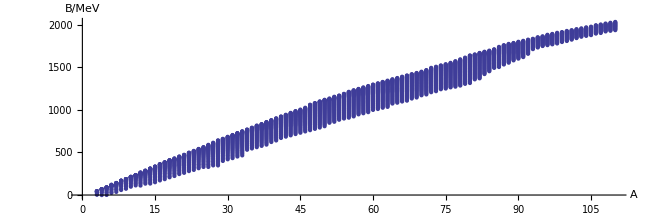

```mathematica
ListPlot[data[[All,{2,4}]],PlotStyle->PointSize[Small],AxesLabel->{A,B/MeV},AspectRatio->1/3]
```

```mathematica
nlm=NonlinearModelFit[data,av A-as A^(2/3)-ac Z^2 A^(-1/3)-aa (A/2-Z)^2 A^-1+ap δ A^(-1/2),{av,as,ac,aa,ap},{A,Z,δ}]
```

FittedModel[-15.9112 A^(2/3)+«19» A-«1»-«1»+(«18» δ)/(√A)]

```mathematica
nlm[{"BestFit","ParameterTable"}]
```

{-15.9112 A^(2/3)+15.2384 A-(89.4082 (A/2-Z)^2)/A-(0.685841 Z^2)/A^(1/3)+(10.2159 δ)/(√A), | Estimate | Standard Error | t-Statistic | P-Value
av | 15.2384 | 0.0195378 | 779.943 | 9.7108574153×10^-3574
as | 15.9112 | 0.0608003 | 261.696 | 5.0433873202×10^-2123
ac | 0.685841 | 0.00137146 | 500.081 | 2.1623893375×10^-2977
aa | 89.4082 | 0.193486 | 462.091 | 6.2403356829×10^-2872
ap | 10.2159 | 0.853191 | 11.9738 | 2.47077×10^-32}

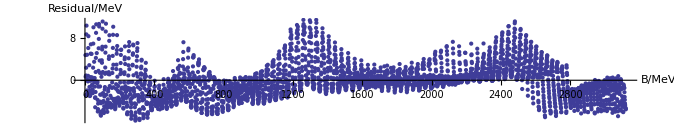

```mathematica
ListPlot[nlm["FitResiduals"],PlotStyle->PointSize[Small],AxesLabel->{B/MeV,Residual/MeV},AspectRatio->1/5]
```